# SAC

### data reading

```mathematica
p0s={3.80,3.825,3.85}
```

{3.8,3.825,3.85}

```mathematica
temperatures={{0.063, 0.039, 0.03105 ,0.025, 0.016, 0.01 ,0.008, 0.0063 ,0.005, 0.00385 ,0.0031 ,0.0028},{0.063,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015,0.001},{0.039, 0.016 ,0.01 ,0.005, 0.00385 ,0.0025, 0.002, 0.001, 0.0005, 0.00033, 0.00025 ,0.00014 ,0.000091, 0.000077,0.000054, 0.000045 ,0.000036}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{1, 3, 4,8, 15, 40,70,150, 250, 600,2000 ,2500},{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000},{2 ,4,10, 20, 40,60, 80,200, 500 ,800 ,1400, 2500 ,4200 ,5000, 6000,8500, 9500}};
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

```mathematica
SACtime=
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p","/SACtime_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10],records[[p,rec]]},{3,4,8,0,0}],"Data"],{rec,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.800/SACtime_N4096_p3.8000_T0.06300000_waitingTime10000_idx14.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.800/SACtime_N4096_p3.8000_T0.06300000_waitingTime10000_idx15.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.800/SACtime_N4096_p3.8000_T0.06300000_waitingTime10000_idx17.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
Table[Table[Table[Length[SACtime[[p,T,rec,2]]],{rec,Length[records[[p]]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

Part::partw: Part 8 of … does not exist.

Part::partw: Part 9 of … does not exist.

Part::partw: Part 10 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{{143,143,143,143,143,143,143,5,5,5},{143,143,143,143,143,143,143,143,5,5},{143,143,143,143,143,143,143,143,143,5},{143,143,143,143,143,143,143,5,5,5},{143,143,143,143,143,143,143,5,5,5},{143,143,143,143,143,143,143,5,5,5},{143,143,143,143,143,143,143,5,5,5},{143,143,143,143,143,143,143,5,5,5},{143,143,143,143,143,143,143,5,5,5},{143,143,143,143,143,143,143,143,5,5},{151,151,151,151,151,151,151,5,5,5},{153,153,5,5,5,5,5,5,5,5}},{{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{147,147,147,147,147,147,147,147,147,147}},{{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{143,143,143,143,143,143,143,143,143,143},{146,146,146,146,146,146,146,146,146,146},{153,153,153,153,153,153,153,153,153,153},{160,160,160,160,160,160,160,160,160,160},{322,322,322,322,322,322,322,322,322,322},{324,324,324,324,324,324,324,324,324,324},{329,329,329,329,329,329,329,329,5,5},{330,330,330,330,330,330,330,330,330,5}}}

```mathematica
time=Normal[SACtime[[3,13,1,2]]]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.36,0.4,0.44,0.48,0.52,0.56,0.6,0.64,0.72,0.8,0.88,0.96,1.04,1.12,1.2,1.28,1.44,1.6,1.76,1.92,2.08,2.24,2.4,2.56,2.88,3.2,3.52,3.84,4.16,4.48,4.8,5.12,5.76,6.4,7.04,7.68,8.32,8.96,9.6,10.24,11.52,12.8,14.08,15.36,16.64,17.92,19.2,20.48,23.04,25.6,28.16,30.72,33.28,35.84,38.4,40.96,46.08,51.2,56.32,61.44,66.56,71.68,76.8,81.92,92.16,102.4,112.64,122.88,133.12,143.36,153.6,163.84,184.32,204.8,225.28,245.76,266.24,286.72,307.2,327.68,368.64,409.6,450.56,491.52,532.48,573.44,614.4,655.36,737.28,819.2,901.12,983.04,1064.96,1146.88,1228.8,1310.72,1474.56,1638.4,1802.24,1966.08,2129.92,2293.76,2457.6,2621.44,2949.12,3276.8,3604.48,3932.16,4259.84,4587.52,4915.2,5242.88,5898.24,6553.6,7208.96,7864.32,8519.68,9175.04,9830.4,10485.8,11796.5,13107.2,14417.9,15728.6,17039.4,18350.1,19660.8,20971.5,23593.,26214.4,28835.8,31457.3,34078.7,36700.2,39321.6}

```mathematica
SACtimeMean=Table[Table[Table[Mean[DeleteCases[Table[SACtime[[p,T,i,1,rec]],{i,Length[SACtime[[p,T]]]}],_Missing|_Part]],{rec,Max[Table[Length[SACtime[[p,T,i,1]]],{i,Length[SACtime[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

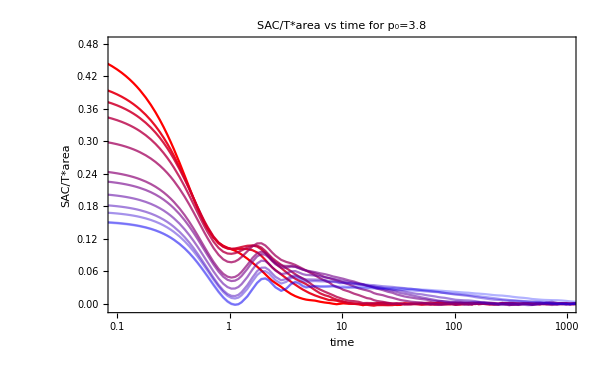
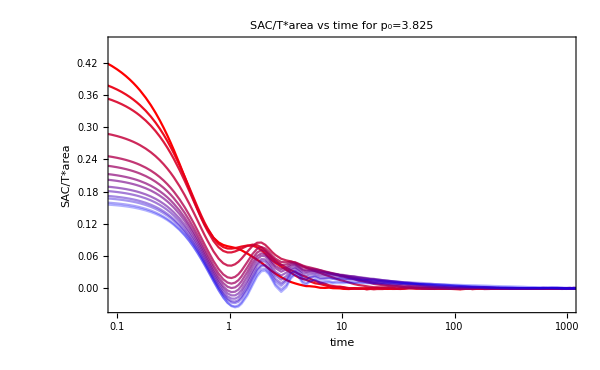
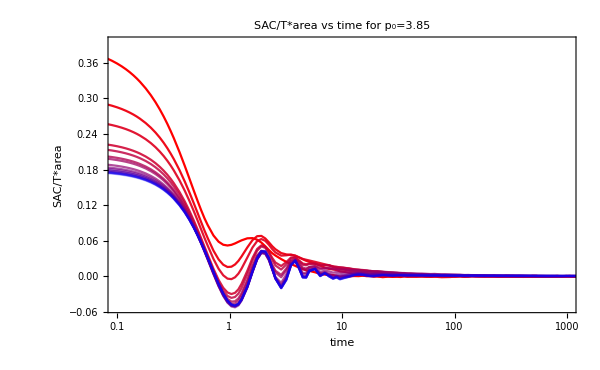

```mathematica
gt=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],SACtimeMean[[p,T,rec]]*4096/temperatures[[p,T]]},{rec,Min[Length[SACtimeMean[[p,T]]],Length[time]]}],{T,1,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","SAC/T*area "},ImageSize->600,PlotLabel->"SAC/T*area vs time for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{{0.1,1000},All}],{p,Length[p0s]}]
```

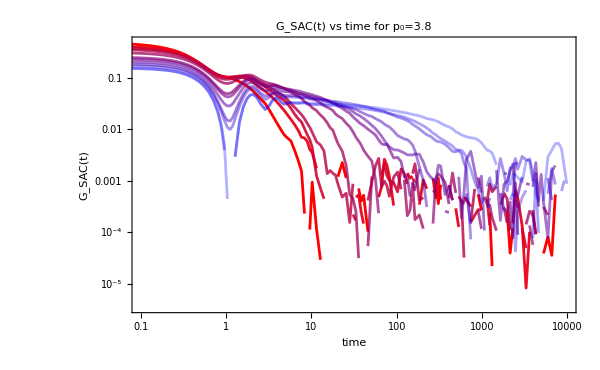
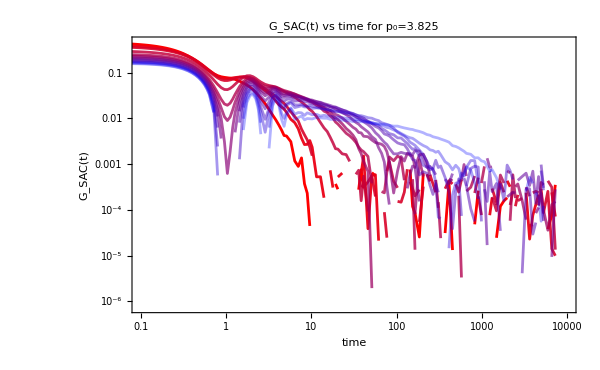
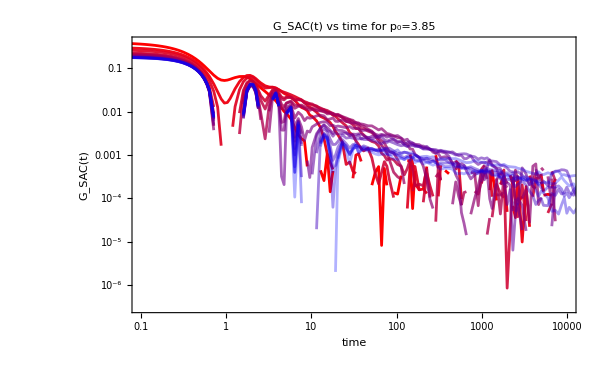

```mathematica
gtlogFull=Table[
ListLogLogPlot[Table[Table[{time[[rec]],SACtimeMean[[p,T,rec]]*4096/temperatures[[p,T]]},{rec,Min[Length[SACtimeMean[[p,T]]],Length[time]]}],{T,1,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Ceiling[Length[temperatures[[p]]]]],FrameLabel->{"time","G_SAC(t) "},ImageSize->600,PlotLabel->"G_SAC(t) vs time for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{{0.1,10000},All}],{p,Length[p0s]}]
```

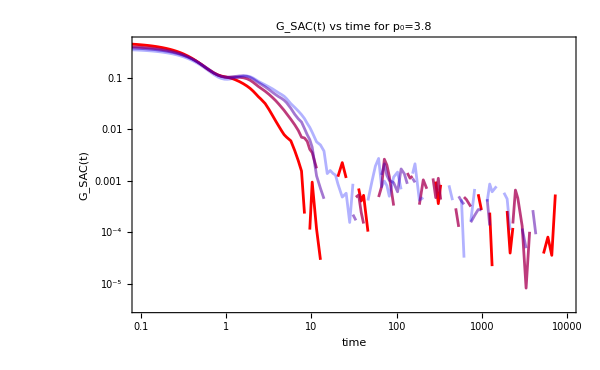
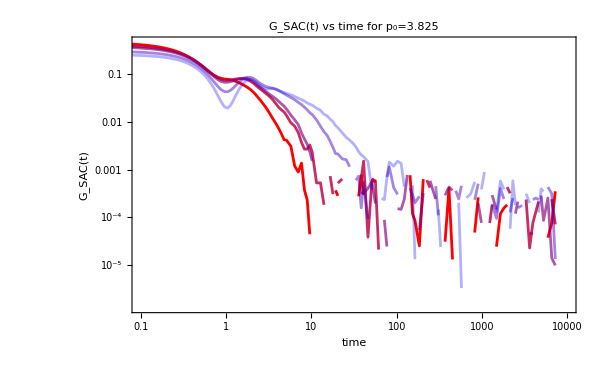
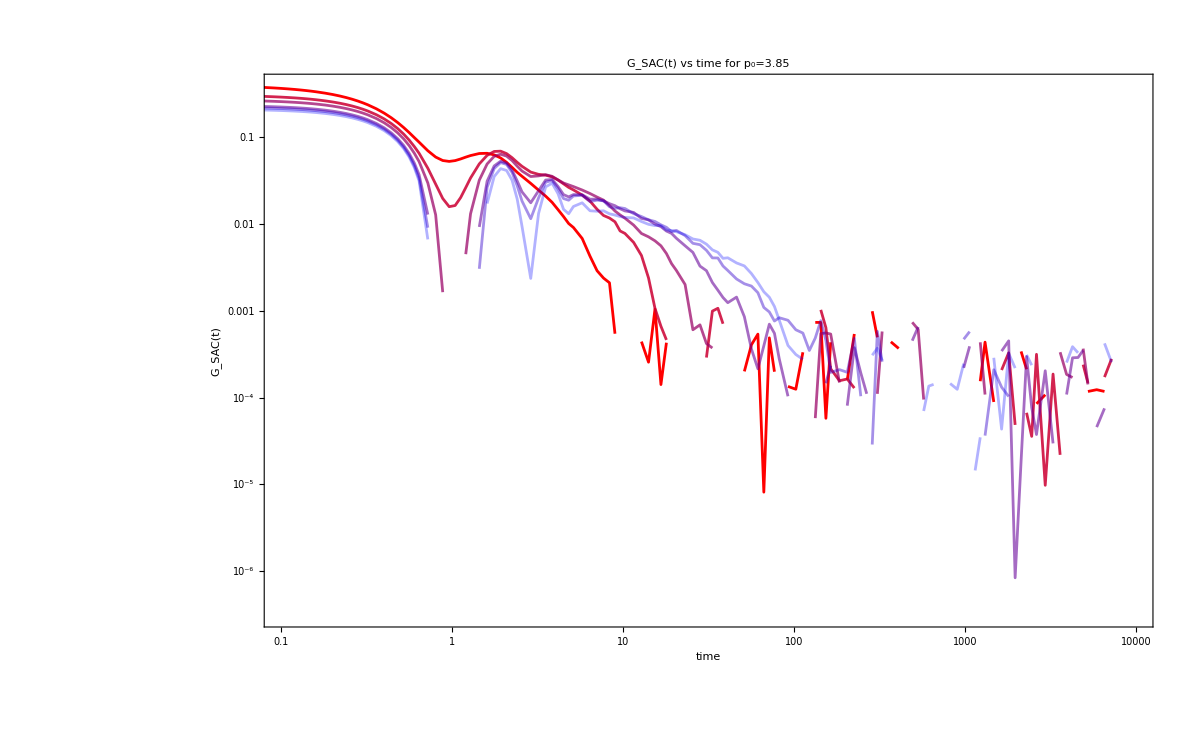

```mathematica
gtlogThirds=Table[
ListLogLogPlot[Table[Table[{time[[rec]],SACtimeMean[[p,T,rec]]*4096/temperatures[[p,T]]},{rec,Min[Length[SACtimeMean[[p,T]]],Length[time]]}],{T,1,Ceiling[Length[temperatures[[p]]]/3]}],PlotStyle->redBluePlotConfig[Ceiling[Length[temperatures[[p]]]/3]],FrameLabel->{"time","G_SAC(t) "},ImageSize->600,PlotLabel->"G_SAC(t) vs time for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{{0.1,10000},All}],{p,Length[p0s]}]
```

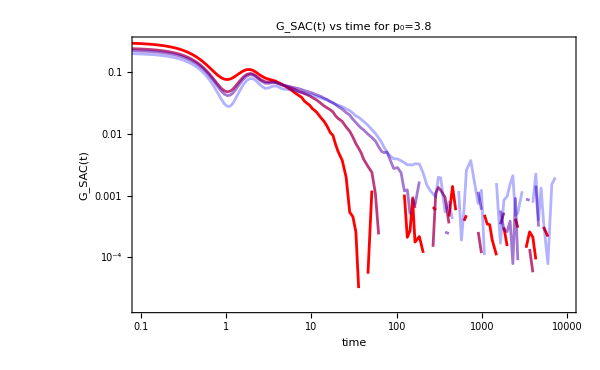
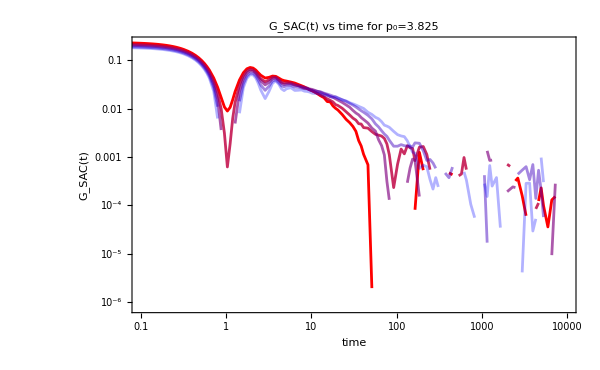
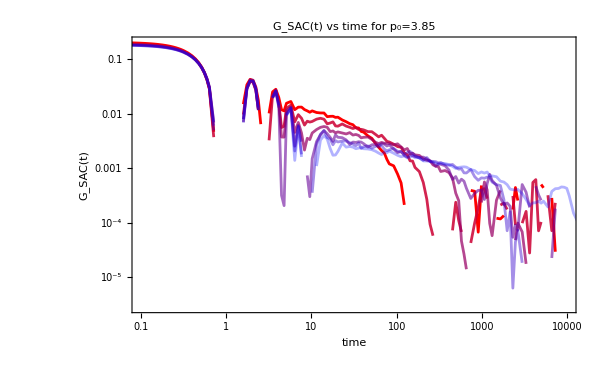

```mathematica
gtlog2Thirds=Table[
ListLogLogPlot[Table[Table[{time[[rec]],SACtimeMean[[p,T,rec]]*4096/temperatures[[p,T]]},{rec,Min[Length[SACtimeMean[[p,T]]],Length[time]]}],{T,Ceiling[Length[temperatures[[p]]]/3]+1,2*Ceiling[Length[temperatures[[p]]]/3]}],PlotStyle->redBluePlotConfig[Ceiling[Length[temperatures[[p]]]/3]],FrameLabel->{"time","G_SAC(t) "},ImageSize->600,PlotLabel->"G_SAC(t) vs time for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{{0.1,10000},All}],{p,Length[p0s]}]
```

```mathematica
GSAC=Table[Table[SACtimeMean[[p,T]]*4096/temperatures[[p,T]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
Dimensions[GSAC[[3]]]
```

{17}

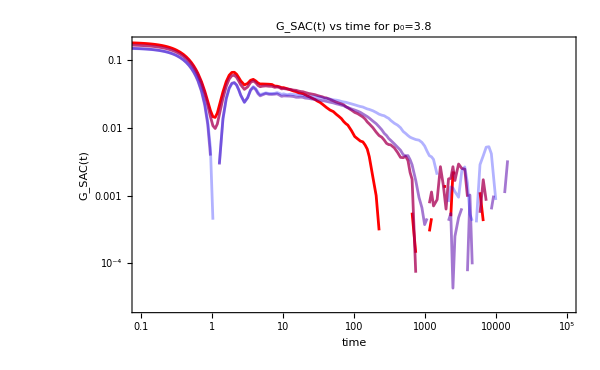
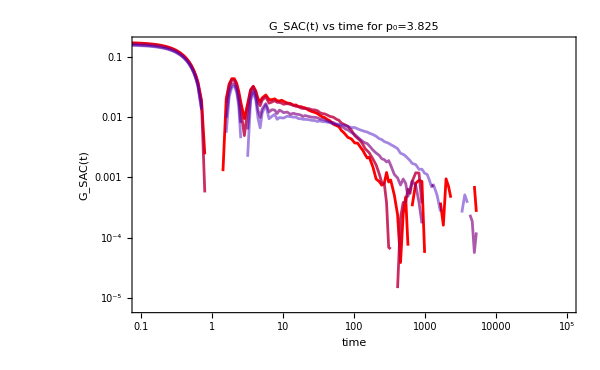
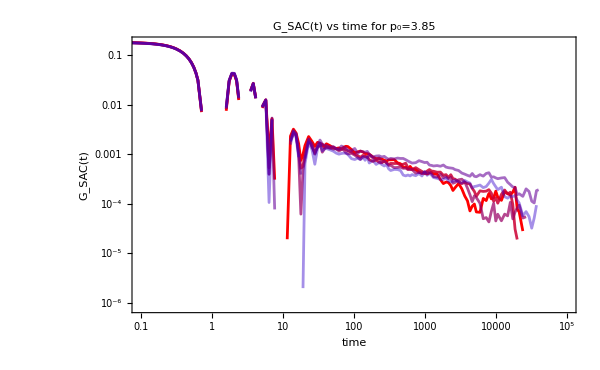

```mathematica
gtlog3Thirds=Table[
ListLogLogPlot[Table[Table[{time[[rec]],SACtimeMean[[p,T,rec]]*4096/temperatures[[p,T]]},{rec,Min[Length[SACtimeMean[[p,T]]],Length[time]]}],{T,2*Ceiling[Length[temperatures[[p]]]/3]+1,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Ceiling[Length[temperatures[[p]]]/3]],FrameLabel->{"time","G_SAC(t) "},ImageSize->600,PlotLabel->"G_SAC(t) vs time for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{{0.1,100000},All}],{p,Length[p0s]}]
```

```mathematica
Dimensions[GSAC[[3,16]]]
```

{326}

```mathematica
fittingStartNum={{1.013099931280425,2.3167655011008437,2.5137463886833467,2.618074726319736,4.632932593585648,4.632865640546632,4.595191464420492,4.595191464420492,5.780745952062278,5.73440793124002,10,10},{1.413730844149886,2.5023682170290185,3.2219788775659173,5.048169204203188,5.522721189600536,5.777215817704034,6.974215721256916,8.417596124525721,9.914186334538392,9.914186334538392,8,8,8,8},{2.6039374675345783,4.578740214874889,4.928532041764077,6.892327365342155,7.006009029615805,8,15.707093523710972,21.780390455069067,24.221768902639027,30.201985342427978,30.951608953260216,32.77388687342174,22,22,22,22,22}};
```

```mathematica
fitStartPos=Table[Table[Position[time,_?(#>fittingStartNum[[p,i]]&)][[1,1]],{i,Length[fittingStartNum[[p]]]}],{p,Length[p0s]}]
```

{{38,48,49,50,56,56,56,56,59,58,65,65},{42,49,52,57,58,59,60,63,65,65,62,62,62,62},{50,56,57,60,60,62,70,74,75,77,78,78,74,74,74,74,74}}

```mathematica
GSAC[[3,17,158;;]]
```

{0.0000515783,0.0000937204,-0.0000208248,0.0000262657,0.17745,0.177395,0.177242,0.176989,0.176638,0.176189,0.175643,0.174999,0.174258,0.173422,0.172491,0.171466,0.170347,0.169136,0.167834,0.166443,0.164941,0.161721,0.158165,0.154285,0.150096,0.145614,0.140854,0.135835,0.130518,0.11936,0.107474,0.0950324,0.08221,0.0691868,0.0561425,0.0432543,0.030817,0.00739716,-0.0129163,-0.0292007,-0.0408251,-0.0474809,-0.0491905,-0.0462925,-0.0386205,-0.016947,0.00893025,0.0308903,0.042942,0.0426517,0.0314484,0.0138083,-0.00311977,-0.0201093,-0.00620939,0.0185275,0.0266535,0.0136547,-0.00173127,-0.00217547,0.00885234,0.0122436,0.000295732,0.00521595,-0.0000678606,-0.00392814,-0.00199669,-0.00537288,-0.00355567,-0.00107719,0.00147084,0.00276232,0.00226293,0.000942037,-0.000221495,9.15014×10^-6,0.000681741,0.00185026,0.00132023,0.000640622,0.00134079,0.00165897,0.00131739,0.00124457,0.00131482,0.00116368,0.00125042,0.00113056,0.00110983,0.00118478,0.00113258,0.00117093,0.0011026,0.000960708,0.000899164,0.000952224,0.000899495,0.00092104,0.000924168,0.000920301,0.00077382,0.000814155,0.000758939,0.00075457,0.000679441,0.000660051,0.000661174,0.000596416,0.000600077,0.000593465,0.000589893,0.000547851,0.000501438,0.000468079,0.000466003,0.000514919,0.00050958,0.000471489,0.000476074,0.000453687,0.000485298,0.000442763,0.000425876,0.000426579,0.000386824,0.000378032,0.000381235,0.000374029,0.000382843,0.000349553,0.000348881,0.000359253,0.000374807,0.000365816,0.000346923,0.000341375,0.000331984,0.000320741,0.00031412,0.000300367,0.000308242,0.000307353,0.000296566,0.000285108,0.000257018,0.000284227,0.000247648,0.000228051,0.000209108,0.000202972,0.000168999,0.00012425,0.0000969394,0.000100484,0.000101861,0.0000729035,0.0000404046,7.55173×10^-6,-3.17065×10^-6,-0.0000199006,-0.0000322446,-0.0000416959,-0.0000731542,-0.000106907,-0.000101636,-0.0000754118,-0.0000738702,-0.00011327,-0.000163448,-0.000133671}

```mathematica
negativePos=Table[Table[If[AllTrue[GSAC[[p,i,fitStartPos[[p,i]];;If[Length[GSAC[[p,i]]]>Length[time],Length[time],Length[GSAC[[p,i]]]]]],#>0&],If[Length[GSAC[[p,i]]]>Length[time],Length[time],Length[GSAC[[p,i]]]],Position[GSAC[[p,i,fitStartPos[[p,i]];;]],_?(#<0&)][[1,1]]+fitStartPos[[p,i]]-2],{i,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{62,66,68,77,79,85,95,108,100,114,118,122},{64,68,65,76,83,83,101,89,103,104,111,105,116,123},{63,71,78,90,101,92,93,102,113,132,130,150,154,152,155,160,159}}

```mathematica
Table[Table[If[Length[GSAC[[p,T]]]>Length[time],Length[time],Length[GSAC[[p,T]]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]-negativePos
```

{{78,74,72,63,61,55,45,32,40,26,30,28},{76,72,75,64,57,57,39,51,37,36,29,35,24,21},{77,69,62,50,39,48,47,38,27,8,13,0,3,8,5,0,1}}

```mathematica
noiseUpperBond={0.007,0.002,0.0000001};
```

```mathematica
noiseMax=Table[Table[Max[Flatten[{Abs[GSAC[[p,T,negativePos[[p,T]];;If[Length[GSAC[[p,T]]]>Length[time],Length[time],Length[GSAC[[p,T]]]]]]],noiseUpperBond[[p]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.007,0.007,0.007,0.007,0.007,0.007,0.007,0.007,0.007,0.007,0.007,0.007},{0.002,0.002,0.002,0.002,0.002,0.002,0.002,0.002,0.002,0.002,0.002,0.002,0.002,0.002},{0.00145481,0.00106259,0.00154201,0.000956995,0.00105068,0.000590327,0.00069074,0.00061828,0.00055946,0.000468204,0.000497637,0.0000637933,0.000191747,0.000207563,0.000132238,0.000191895,0.0000937204}}

```mathematica
GSAC[[3,12,fitStartPos[[3,12]];;If[Length[GSAC[[3,12]]]>Length[time],Length[time],Length[GSAC[[3,12]]]]]]
```

{0.00227732,0.0023409,0.00238112,0.00227589,0.00225072,0.00218307,0.00205468,0.00189639,0.00178098,0.00198273,0.00192598,0.00205901,0.00188374,0.0017243,0.00162351,0.00167647,0.00154625,0.00160593,0.00167017,0.00155794,0.00156183,0.00136025,0.00135524,0.00132281,0.00129949,0.00124907,0.00118124,0.00123272,0.00121648,0.00116975,0.00108194,0.000991377,0.00103487,0.00105079,0.00106073,0.00104599,0.000942523,0.000905708,0.000797366,0.000853977,0.000814447,0.000851833,0.00072564,0.000722962,0.000698191,0.000579196,0.000557432,0.00049961,0.000414432,0.00040409,0.000396871,0.000408929,0.000341791,0.000268048,0.000208036,0.000232018,0.00023287,0.000250965,0.000228724,0.000249083,0.000195012,0.000376064,0.00042117,0.000425919,0.000454054,0.000448008,0.000426823,0.000312561,0.000149405,0.000106207,0.000190541,0.000180213,0.0000637933}

```mathematica
noiseMax[[3,12]]
```

0.0000637933

```mathematica
Position[GSAC[[3,12,fitStartPos[[3,12]];;If[Length[GSAC[[3,12]]]>Length[time],Length[time],Length[GSAC[[3,12]]]]]],_?(#<noiseMax[[3,12]]&)][[1,1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1,1⟧

```mathematica
fitEndPos=Table[Table[If[AllTrue[GSAC[[p,i,fitStartPos[[p,i]];;If[Length[GSAC[[p,i]]]>Length[time],Length[time],Length[GSAC[[p,i]]]]]],#>=noiseMax[[p,i]]&],If[Length[GSAC[[p,i]]]>Length[time],Length[time],Length[GSAC[[p,i]]]],Position[GSAC[[p,i,fitStartPos[[p,i]];;If[Length[GSAC[[p,i]]]>Length[time],Length[time],Length[GSAC[[p,i]]]]]],_?(#<noiseMax[[p,i]]&)][[1,1]]-2+fitStartPos[[p,i]]],{i,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{56,60,63,65,71,77,84,86,91,101,104,113},{58,65,64,73,80,79,87,85,89,94,97,98,101,111},{62,68,74,82,86,89,91,98,108,112,122,150,127,134,134,151,153}}

```mathematica
Export["/home/chengling/Research/updates/05022024/SAC.jpeg",gt,ImageResolution->800]
```

/home/chengling/Research/updates/05022024/SAC.jpeg

```mathematica
Export["/home/chengling/Research/updates/05022024/SAClog.jpeg",gtlog,ImageResolution->800]
```

/home/chengling/Research/updates/05022024/SAClog.jpeg

### fit to stretched exponential

```mathematica
Table[Length[temperatures[[i]]],{i,3}]
```

{12,14,17}

```mathematica
betaConstrains={{1.0>β>0.80,0.85>β>0.80,0.85>β>0.80,0.85>β>0.80,1.0>β>0.81,1.0>β>0.81,1.0>β>0.81,1.0>β>0.81,1.0>β>0.82,0.95>β>0.8,0.84>β>0.5,0.9>β>0.82},{1.0>β>0.90,0.9>β>0.85,0.9>β>0.85,0.9>β>0.8,1.0>β>0.80,1.0>β>0.85,1.0>β>0.85,1.0>β>0.5,0.85>β>0.5,1.0>β>0.5,1.0>β>0.8,1.0>β>0.5,1.0>β>0.8,1.0>β>0.78},{1.0>β>0.88,1.0>β>0.88,1.0>β>0.88,1.0>β>0.5,1.0>β>0.9,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,0.65>β>0.5,0.65>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5}};
```

```mathematica
{1.0>β>0.5,1.0>β>0.9,1.0>β>0.95,1.0>β>0.95,1.0>β>0.81,1.0>β>0.81,1.0>β>0.81,1.0>β>0.81,1.0>β>0.82,0.95>β>0.8,0.84>β>0.5,0.9>β>0.82}
```

```mathematica
gConstrains={{0.8>G>0.1,0.8>G>0.32,0.8>G>0.28,0.8>G>0.24,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.08>G>0.0001,0.08>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001},{0.8>G>0.3,0.8>G>0.3,0.8>G>0.28,0.8>G>0.13,0.8>G>0.09,0.8>G>0.072,0.8>G>0.06,0.8>G>0.0001,0.038>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.02,0.08>G>0.015,0.08>G>0.010},{0.8>G>0.16,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.01>G>0.009,0.0055>G>0.0001,0.8>G>0.0001,0.003>G>0.001,0.002>G>0.0001,0.8>G>0.001,0.8>G>0.001,0.8>G>0.001,0.8>G>0.001,0.8>G>0.001}};
```

```mathematica
fits=Table[Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[GSAC[[p,T,rec]]]},{rec,fitStartPos[[p,T]],fitEndPos[[p,T]]}],{stretchedExp[t,G,τ,β],{betaConstrains[[p,T]],gConstrains[[p,T]],τ>0.5}},{G,τ,β},t],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
plateauSISFfits=Table[Table[Around[fits[[p,T]]["BestFitParameters"][[1,2]],fits[[p,T]]["ParameterErrors"][[1]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

{{0.2090.026,0.320.12,0.280.10,0.240.05,0.1610.015,0.10060.0035,0.08510.0016,0.06930.0010,0.05310.0011,0.04470.0006,0.032630.00026,0.032830.00033},{0.300.13,0.300.18,0.280.30,0.1320.024,0.0900.008,0.0730.005,0.0600.011,0.04650.0015,0.03790.0018,0.03100.0013,0.02420.0009,0.02050.0005,0.01500.0006,0.010490.00015},{0.170.04,0.0890.030,0.0670.012,0.03490.0031,0.02830.0030,0.01950.0010,0.01650.0014,0.00940.0010,0.00520.0004,0.00390.0004,0.002850.00020,0.001970.00015,0.002090.00022,0.001620.00017,0.001600.00018,0.001500.00012,0.001420.00020}}

```mathematica
betaSISFfitsTable=Table[Table[Around[fits[[p,T]]["BestFitParameters"][[3,2]],fits[[p,T]]["ParameterErrors"][[3]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

{{1.000.10,0.800.14,0.800.16,0.800.10,0.820.05,0.8410.030,0.8470.020,0.8160.018,0.8220.028,0.8010.025,0.8320.018,0.8210.024},{0.900.18,0.850.21,0.850.33,0.840.08,0.800.05,0.860.04,0.850.12,0.8550.025,0.850.04,0.810.04,0.810.04,0.840.04,0.800.06,0.7930.033},{0.900.09,0.940.18,0.900.10,0.940.07,0.910.09,0.840.05,0.920.07,0.820.10,0.780.09,0.690.10,0.710.10,0.610.10,0.550.08,0.550.10,0.560.10,0.530.09,0.550.12}}

```mathematica
tauSISFfitsTable=Table[Table[Around[fits[[p,T]]["BestFitParameters"][[2,2]],fits[[p,T]]["ParameterErrors"][[2]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

{{1.520.20,1.40.5,1.90.8,2.40.6,5.00.6,10.90.5,18.30.5,25.30.5,44.41.3,108.42.3,196.22.2,349.6.},{1.00.4,1.30.7,1.51.4,3.90.7,6.60.7,8.80.7,11.32.5,17.80.7,25.61.6,34.72.1,45.42.4,71.12.4,90.5.,283.7.},{1.530.33,3.91.2,5.61.0,11.91.2,16.12.1,23.61.7,30.83.0,71.10.,160.19.,221.36.,513.64.,1489.261.,339.78.,588.144.,513.131.,1915.392.,551.181.}}

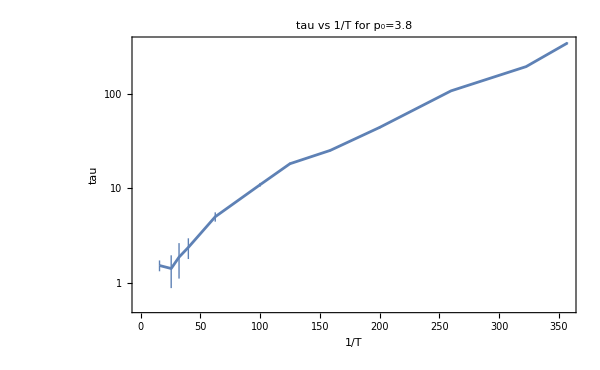
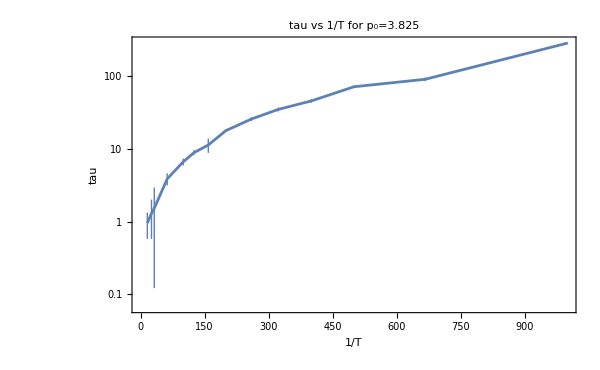
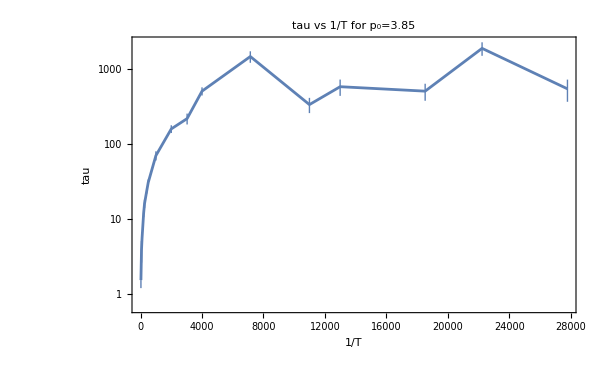

```mathematica
plateauPlots=Table[ListLogPlot[Table[{1/temperatures[[p,T]],tauSISFfitsTable[[p,T]]},{T,Length[temperatures[[p]]]}],FrameLabel->{"1/T","tau "},ImageSize->600,PlotLabel->"tau vs 1/T for p_0="<>ToString[p0s[[p]]],Joined->True],{p,Length[p0s]}]
```

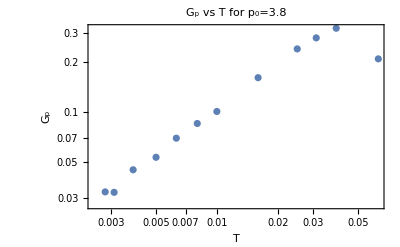
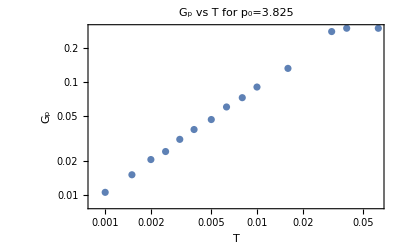
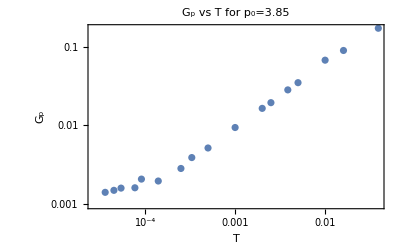

```mathematica
Table[ListLogLogPlot[Table[{temperatures[[p,T]],plateauSISFfits[[p,T,1]]},{T,Length[temperatures[[p]]]}],FrameLabel->{"T","G_p "},ImageSize->400,PlotLabel->"G_p vs T for p_0="<>ToString[p0s[[p]]]],{p,Length[p0s]}]
```

```mathematica
-
```

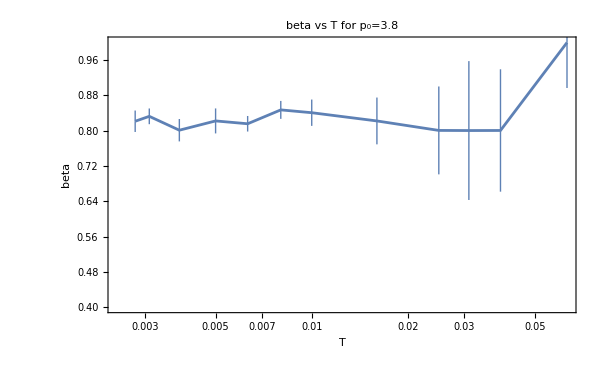
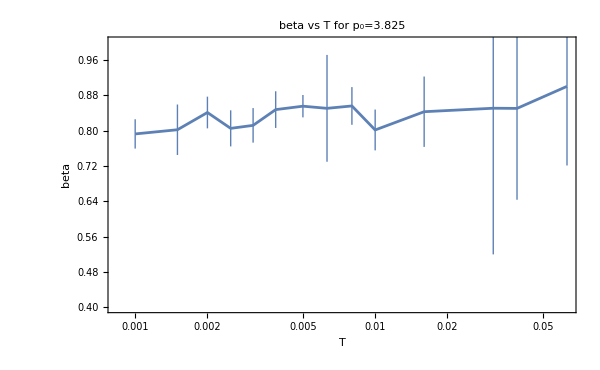
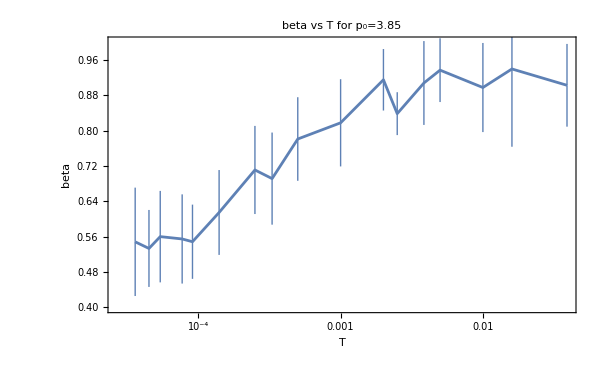

```mathematica
betaPlots=Table[ListLogLinearPlot[Table[{temperatures[[p,T]],betaSISFfitsTable[[p,T]]},{T,Length[temperatures[[p]]]}],Joined->True,PlotRange->{All,{0.4,1.0}},FrameLabel->{"T","beta"},ImageSize->600,PlotLabel->"beta vs T for p_0="<>ToString[p0s[[p]]]],{p,Length[p0s]}]
```

```mathematica
niceStretchedExp={{0,1,1,1,1,1,1,1,1,1,1,0},{0,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0}};
```

```mathematica
niceStretchedExpStartEnd={{2,11},{2,14},{4,12}};
```

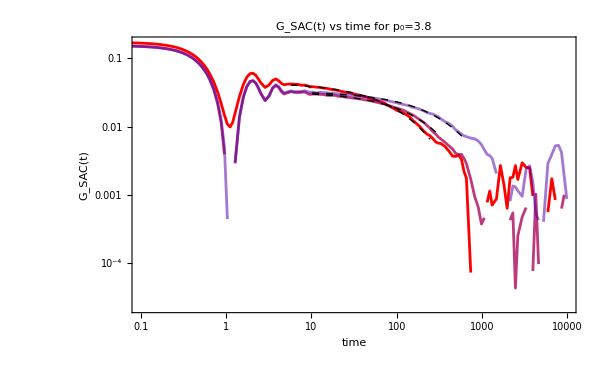
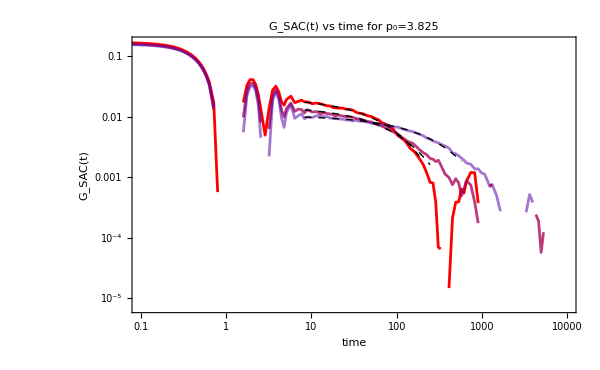
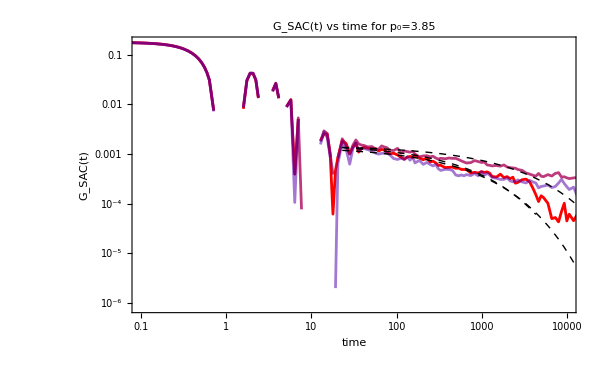

```mathematica
Table[Show[
ListLogLogPlot[Table[Table[{time[[rec]],GSAC[[p,T,rec]]},{rec,Min[Length[GSAC[[p,T]]],Length[time]]}],{T,Length[temperatures[[p]]]-2,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[4],FrameLabel->{"time","G_SAC(t) "},ImageSize->600,PlotLabel->"G_SAC(t) vs time for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{{0.1,10000},All}],Table[LogLogPlot[fits[[p,T]][x],{x,time[[fitStartPos[[p,T]]]],time[[fitEndPos[[p,T]]]]},PlotStyle->{Dashed,Thick,Black}],{T,Length[temperatures[[p]]]-2,Length[temperatures[[p]]]}]],{p,1,3}]
```

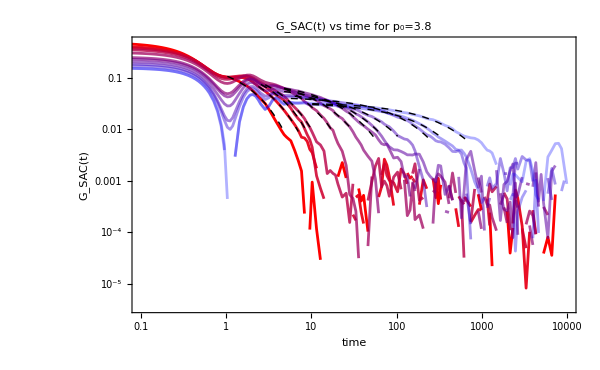
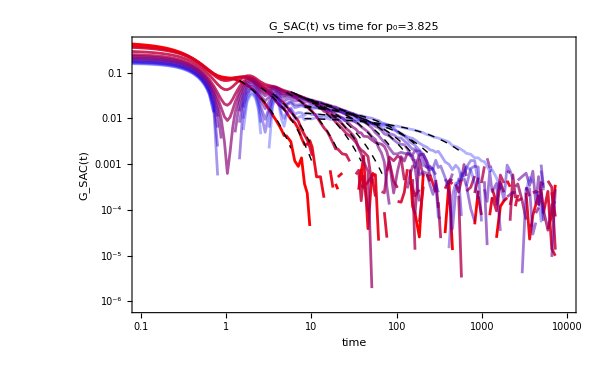
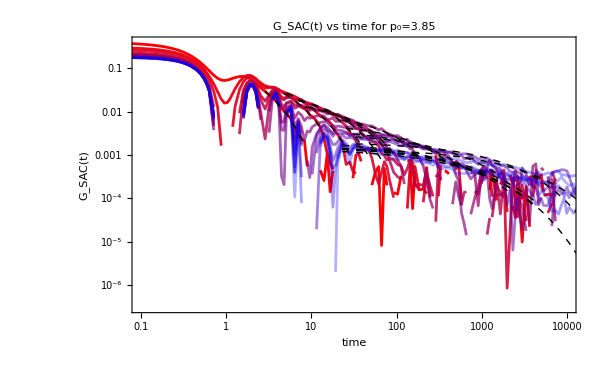

```mathematica
fitsPlots=Table[Show[
ListLogLogPlot[Table[Table[{time[[rec]],GSAC[[p,T,rec]]},{rec,Min[Length[GSAC[[p,T]]],Length[time]]}],{T,1,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","G_SAC(t) "},ImageSize->600,PlotLabel->"G_SAC(t) vs time for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{{0.1,10000},All}],Table[LogLogPlot[fits[[p,T]][x],{x,time[[fitStartPos[[p,T]]]],time[[fitEndPos[[p,T]]]]},PlotStyle->{Dashed,Thick,Black}],{T,1,Length[temperatures[[p]]]}]],{p,Length[p0s]}]
```

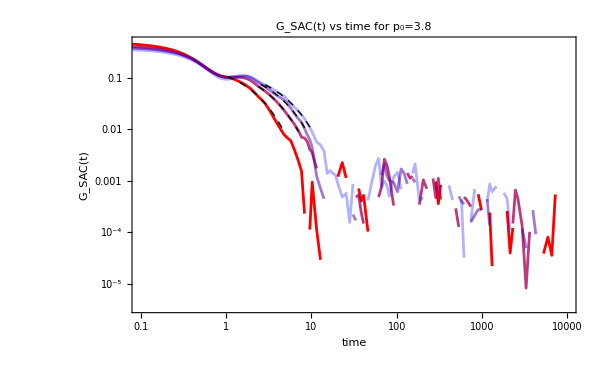
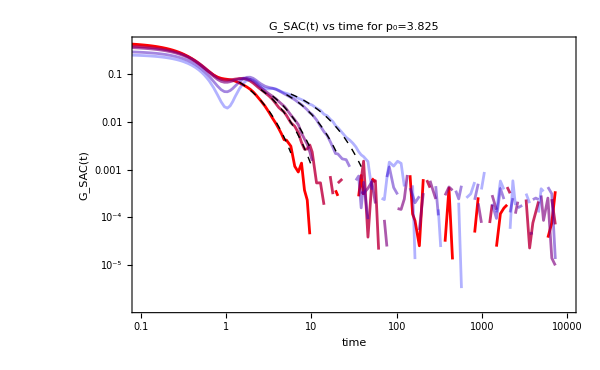
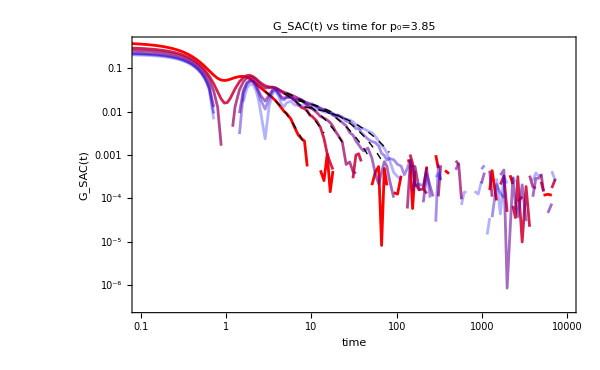
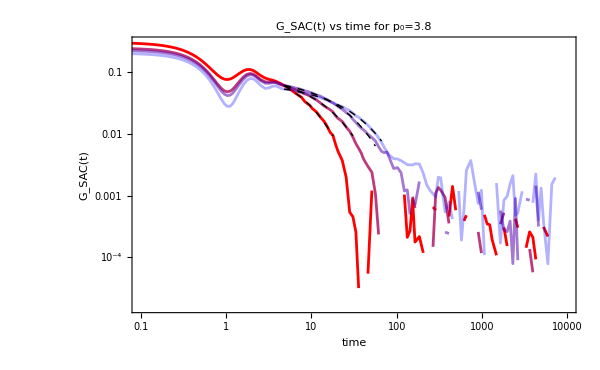
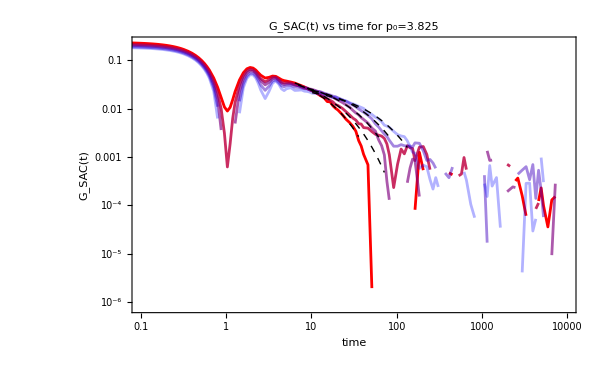
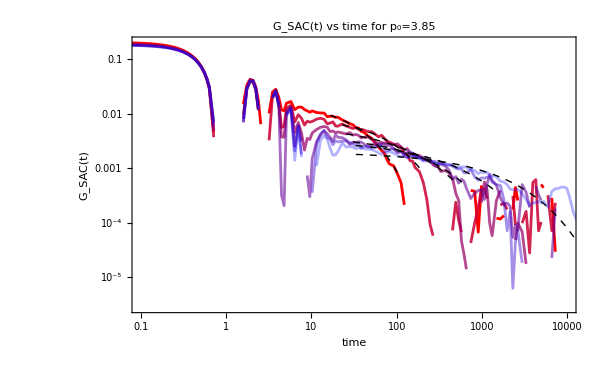
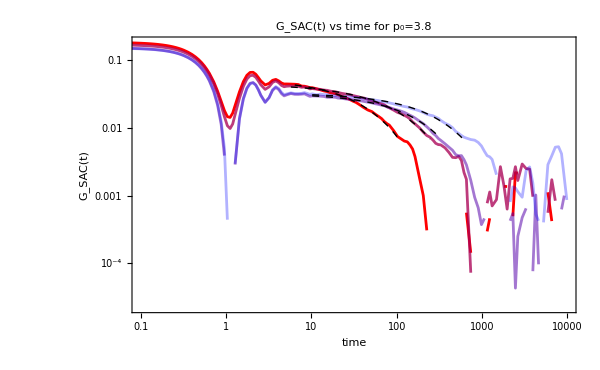
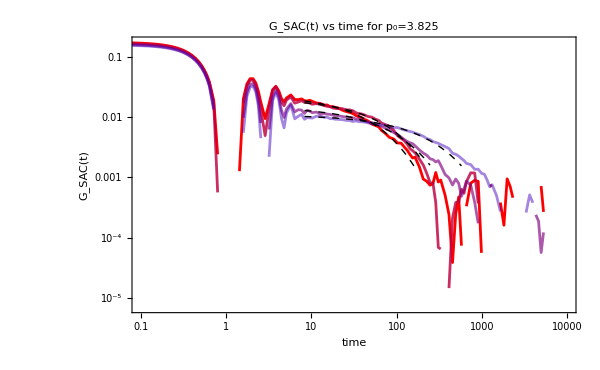

```mathematica
fitsPlots={Table[Show[
ListLogLogPlot[Table[Table[{time[[rec]],GSAC[[p,T,rec]]},{rec,Min[Length[GSAC[[p,T]]],Length[time]]}],{T,1,Ceiling[Length[temperatures[[p]]]/3]}],PlotStyle->redBluePlotConfig[Ceiling[Length[temperatures[[p]]]/3]],FrameLabel->{"time","G_SAC(t) "},ImageSize->600,PlotLabel->"G_SAC(t) vs time for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{{0.1,10000},All}],Table[LogLogPlot[fits[[p,T]][x],{x,time[[fitStartPos[[p,T]]]],time[[fitEndPos[[p,T]]]]},PlotStyle->{Dashed,Black,Thick},PlotStyle->redBluePlotConfig[Ceiling[Length[temperatures[[p]]]/3]]],{T,1,Ceiling[Length[temperatures[[p]]]/3]}]],{p,Length[p0s]}],Table[Show[
ListLogLogPlot[Table[Table[{time[[rec]],GSAC[[p,T,rec]]},{rec,Min[Length[GSAC[[p,T]]],Length[time]]}],{T,Ceiling[Length[temperatures[[p]]]/3]+1,2*Ceiling[Length[temperatures[[p]]]/3]}],PlotStyle->redBluePlotConfig[Ceiling[Length[temperatures[[p]]]/3]],FrameLabel->{"time","G_SAC(t) "},ImageSize->600,PlotLabel->"G_SAC(t) vs time for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{{0.1,10000},All}],Table[LogLogPlot[fits[[p,T]][x],{x,time[[fitStartPos[[p,T]]]],time[[fitEndPos[[p,T]]]]},PlotStyle->{Dashed,Black,Thick},PlotStyle->redBluePlotConfig[Ceiling[Length[temperatures[[p]]]/3]]],{T,Ceiling[Length[temperatures[[p]]]/3]+1,2*Ceiling[Length[temperatures[[p]]]/3]}]],{p,Length[p0s]}],Table[Show[
ListLogLogPlot[Table[Table[{time[[rec]],GSAC[[p,T,rec]]},{rec,Min[Length[GSAC[[p,T]]],Length[time]]}],{T,2*Ceiling[Length[temperatures[[p]]]/3]+1,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Ceiling[Length[temperatures[[p]]]/3]],FrameLabel->{"time","G_SAC(t) "},ImageSize->600,PlotLabel->"G_SAC(t) vs time for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{{0.1,10000},All}],Table[LogLogPlot[fits[[p,T]][x],{x,time[[fitStartPos[[p,T]]]],time[[fitEndPos[[p,T]]]]},PlotStyle->{Dashed,Thick,Black}],{T,2*Ceiling[Length[temperatures[[p]]]/3]+1,Length[temperatures[[p]]]}]],{p,Length[p0s]}]}
```

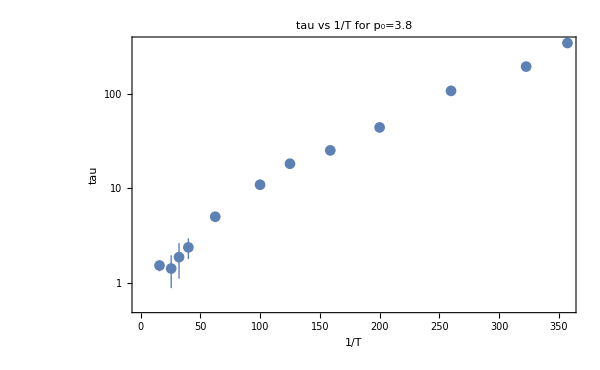
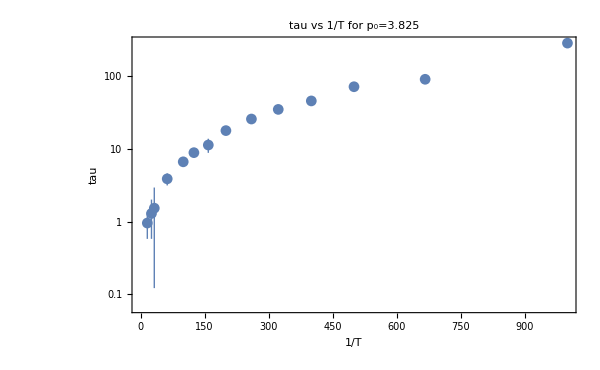
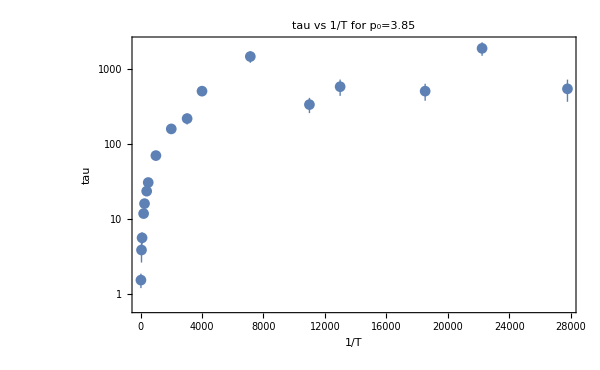

```mathematica
tauPlots=Table[ListLogPlot[Table[{1/temperatures[[p,T]],tauSISFfitsTable[[p,T]]},{T,Length[temperatures[[p]]]}],FrameLabel->{"1/T","tau"},ImageSize->600,PlotLabel->"tau vs 1/T for p_0="<>ToString[p0s[[p]]]],{p,Length[p0s]}]
```

```mathematica
Gpfits=Table[NonlinearModelFit[Table[{temperatures[[p,T]],plateauSISFfits[[p,T]]},{T,niceStretchedExpStartEnd[[p,1]],niceStretchedExpStartEnd[[p,2]]}],{A*x^B},{A,B},x],{p,Length[p0s]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[If[niceStretchedExp[[p,T]]==1,"ClosedMarkers","OpenMarkers"],{T,Length[temperatures[[p]]]}],
```

```mathematica
Table[If[niceStretchedExp[[1,T]]==1,"ClosedMarkers","OpenMarkers"],{T,Length[temperatures[[1]]]}]
```

{OpenMarkers,OpenMarkers,OpenMarkers,OpenMarkers,ClosedMarkers,ClosedMarkers,ClosedMarkers,ClosedMarkers,ClosedMarkers,ClosedMarkers,ClosedMarkers,ClosedMarkers}

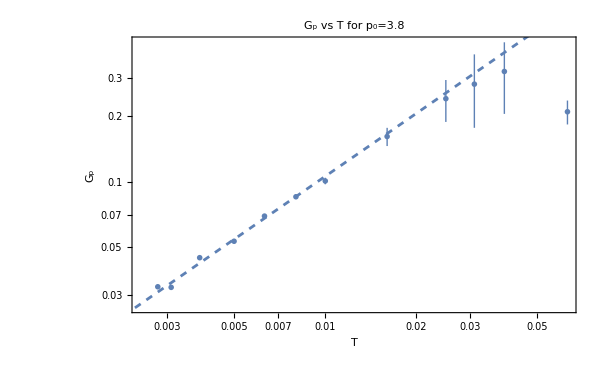
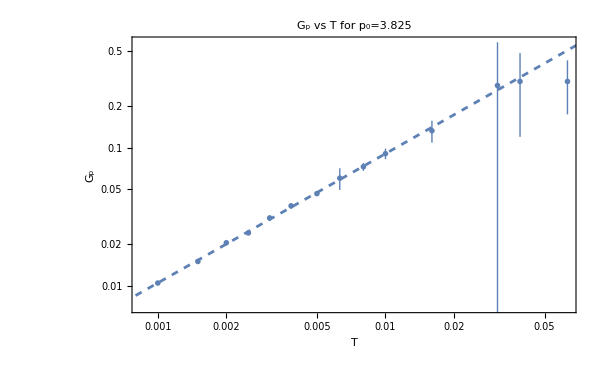
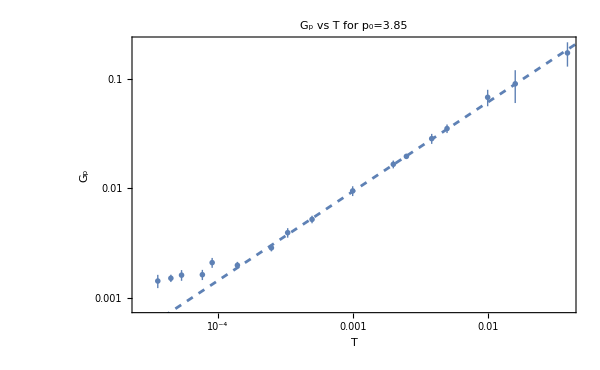

```mathematica
GpPlots=Table[Show[ListLogLogPlot[Table[{temperatures[[p,T]],plateauSISFfits[[p,T]]},{T,Length[temperatures[[p]]]}],FrameLabel->{"T","G_p "},PlotRange->{All,{{All,0.007,All}[[p]],All}},PlotMarkers->Table[If[niceStretchedExp[[p,T]]==1,"ClosedMarkers","OpenMarkers"],{T,Length[temperatures[[p]]]}],ImageSize->600,PlotLabel->"G_p vs T for p_0="<>ToString[p0s[[p]]]],LogLogPlot[Gpfits[[p]][T],{T,0.00001,0.1},PlotStyle->Dashed]],{p,Length[p0s]}]
```

```mathematica
tauFitEnd={4,2,5};
```

```mathematica
taufit=Table[NonlinearModelFit[Table[{1/temperatures[[p,T]],tauSISFfitsTable[[p,T]][[1]]},{T,Length[temperatures[[p]]]-tauFitEnd[[p]]}],{A Exp[B t^(1-Gpfits[[p]]["BestFitParameters"][[2,2]])]},{B,A},t,MaxIterations->1000],{p,Length[p0s]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…]}

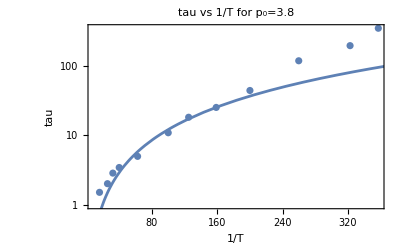
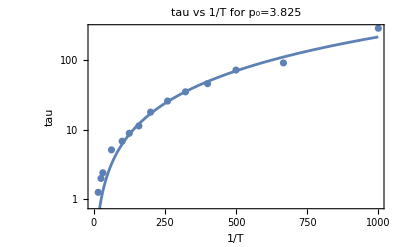
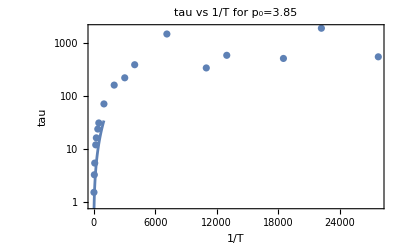

```mathematica
taufitPlots=Table[Show[ListLogPlot[Table[{1/temperatures[[p,T]],tauSISFfitsTable[[p,T]][[1]]},{T,Length[temperatures[[p]]]}],FrameLabel->{"1/T","tau "},ImageSize->400,PlotLabel->"tau vs 1/T for p_0="<>ToString[p0s[[p]]],PlotRange->All,PlotLegends->"Exp[T^-"<>ToString[1-Gpfits[[p]]["BestFitParameters"][[2,2]]]<>"]"],LogPlot[taufit[[p]][t],{t,1,1000}]],{p,1,3}]
```

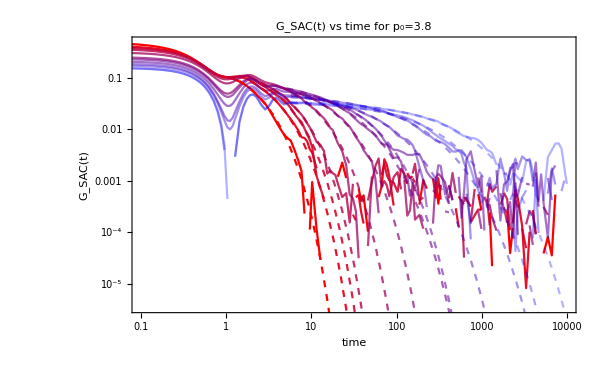
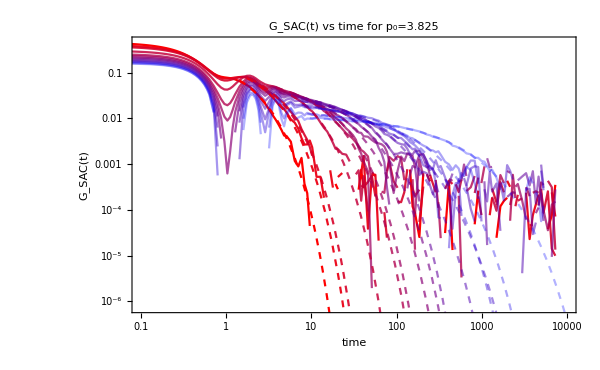
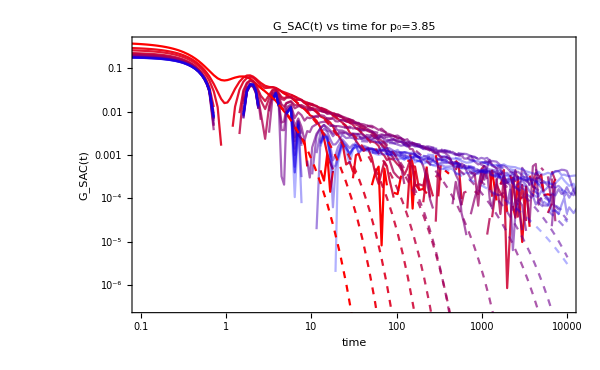

```mathematica
fittingPlotofSAC=Table[Show[gtlogFull[[p]],Table[LogLogPlot[fitsAgain[[p,T]][x],{x,time[[fitStartPos[[p,T]]]],10000},PlotRange->{{0.01,1000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[temperatures[[p]]]][[T]]}],{T,Length[temperatures[[p]]]}]],{p,Length[p0s]}]
```

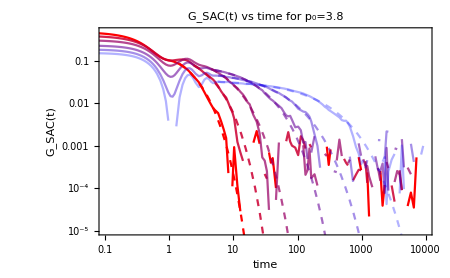
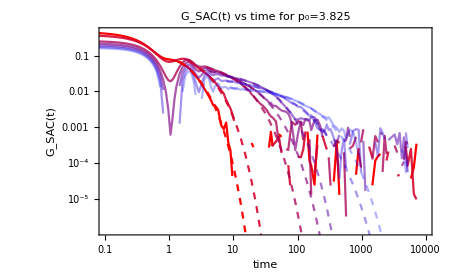
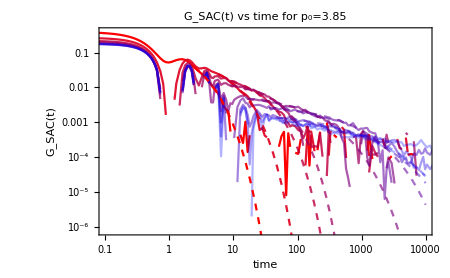

```mathematica
fittingPlotofSACSpacing2=Table[Show[gtlog[[p]],Table[LogLogPlot[fitsAgain[[p,T]][x],{x,time[[fitStartPos[[p,T]]]],10000},PlotRange->{{0.01,1000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Ceiling[Length[temperatures[[p]]]/2]][[(T+1)/2]]}],{T,1,Length[temperatures[[p]]],2}],ImageSize->450],{p,Length[p0s]}]
```

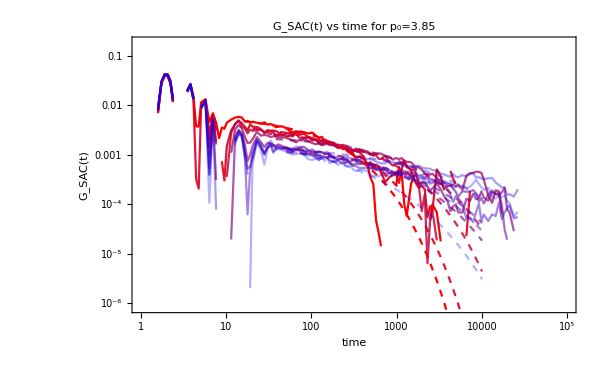

```mathematica
Table[Show[lowTGSAC,Table[LogLogPlot[fitsAgain[[p,T]][x],{x,time[[fitStartPos[[p,T]]]],10000},PlotRange->{{0.01,1000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[temperatures[[p]]]-8][[T-8]]}],{T,9,Length[temperatures[[p]]]}]],{p,3,Length[p0s]}]
```

### fit tau

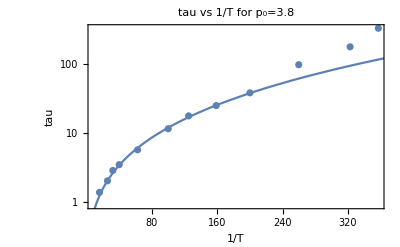
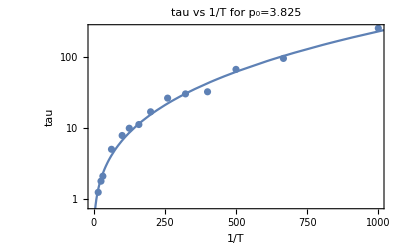
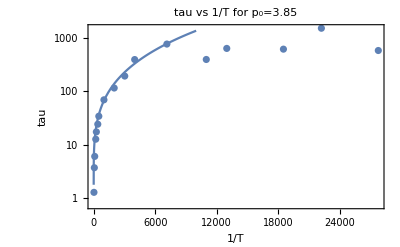

```mathematica
taufitPlots=Table[Show[ListLogPlot[Table[{1/temperatures[[p,T]],fitsAgain[[p,T]]["BestFitParameters"][[2,2]]},{T,Length[temperatures[[p]]]}],FrameLabel->{"1/T","tau "},ImageSize->400,PlotLabel->"tau vs 1/T for p_0="<>ToString[p0s[[p]]],PlotRange->All,PlotLegends->"Exp[T^-"<>ToString[1-Gpfits[[p,2]]["BestFitParameters"][[2,2]]]<>"]"],LogPlot[taufit[[p]][t],{t,0.000001,10000}]],{p,1,3}]
```

```mathematica
end={4,2,5};
```

```mathematica
taufit=Table[NonlinearModelFit[Table[{1/temperatures[[p,T]],fitsAgain[[p,T]]["BestFitParameters"][[2,2]]},{T,Length[temperatures[[p]]]-end[[p]]}],{A Exp[B t^(1-Gpfits[[p,2]]["BestFitParameters"][[2,2]])]},{B,A},t],{p,Length[p0s]}]
```

{FittedModel[0.0219947 ⅇ^(2.07422 t^0.241076)],FittedModel[0.129442 ⅇ^(1.1038 t^0.277283)],FittedModel[1.66466 ⅇ^(0.616035 t^0.258938)]}

```mathematica
Table[NonlinearModelFit[Table[{temperatures[[p,T]],fitsAgain[[p,T]]["BestFitParameters"][[2,2]]},{T,Length[temperatures[[p]]]-6,Length[temperatures[[p]]]-2}],{A Exp[B/t^0.28]},{B,A},t],{p,Length[p0s]}]
```

{FittedModel[0.00218083 ⅇ^(2.25059/t^0.28)],FittedModel[0.108412 ⅇ^(1.11802/t^0.28)],FittedModel[328.295 ⅇ^(0.0394821/t^0.28)]}

```mathematica
Gp=Table[Table[fitsAgain[[p,T]]["BestFitParameters"][[1,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.238988,0.22124,0.18137,0.165778,0.144118,0.0965828,0.0876072,0.0702011,0.0593756,0.0488364,0.035697,0.0353185},{0.210469,0.200275,0.180627,0.100146,0.0777293,0.0645052,0.0586641,0.0477277,0.0366607,0.0337973,0.0294987,0.0211938,0.0147433,0.0113835},{0.207999,0.0940129,0.0631365,0.0326834,0.026236,0.0191781,0.0150667,0.00957655,0.00634461,0.004242,0.00330819,0.00248466,0.00198621,0.00158741,0.00150601,0.00153558,0.0013498}}

```mathematica
tau=Table[Table[fitsAgain[[p,T]]["BestFitParameters"][[2,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{1.39109,2.03771,2.87218,3.48586,5.70239,11.4923,17.5916,24.802,37.8136,96.2754,174.273,323.103},{1.26053,1.81005,2.12858,5.09058,7.95911,10.0752,11.3634,17.1672,26.7434,30.6758,32.8479,67.9058,96.8824,257.807},{1.28721,3.71026,6.03279,12.6338,17.3083,24.0681,33.9305,68.6455,113.991,190.622,387.569,754.296,388.866,625.408,606.03,1489.06,571.821}}

```mathematica
rs=Table[Table[fits[[p,T]]["AdjustedRSquared"],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.999457,0.998257,0.999165,0.999886,0.99797,0.997879,0.996473,0.998653,0.997545,0.999094,0.998818,0.997849,0.99851,0.998825}}

```mathematica
GpfitRange={{{1,5},{6,10}},{{}}}
```

```mathematica
Gpfits=Table[{NonlinearModelFit[Table[{temperatures[[p,T]],Gp[[p,T]]},{T,1,4}],{A*x^B},{A,B},x],NonlinearModelFit[Table[{temperatures[[p,T]],Gp[[p,T]]},{T,5,10}],{A*x^B},{A,B},x]},{p,Length[p0s]}]
```

{{FittedModel[0.706311 x^0.383025],FittedModel[3.30353 x^0.758924]},{FittedModel[0.79098 x^0.453188],FittedModel[2.1692 x^0.722717]},{FittedModel[3.70866 x^0.887974],FittedModel[1.60117 x^0.741062]}}

```mathematica
NonlinearModelFit[Table[{temperatures[[2,T]],Gp[[2,T]]},{T,Length[temperatures[[2]]]-3}],{A*x^B},{A,B},x]
```

FittedModel[1.21328 x^0.592597]

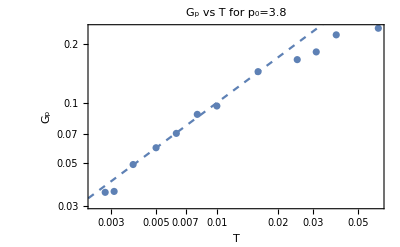
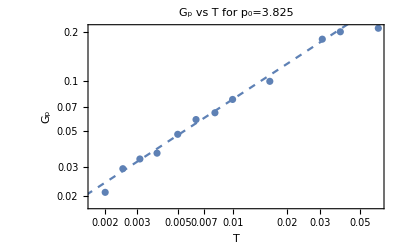
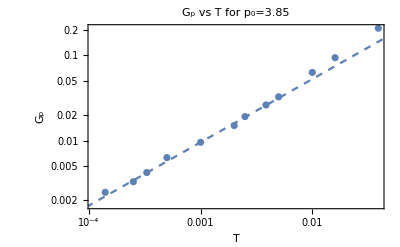

```mathematica
GpPlots=Table[Show[ListLogLogPlot[Table[{temperatures[[p,T]],Gp[[p,T]]},{T,Length[temperatures[[1]]]}],FrameLabel->{"T","G_p "},ImageSize->400,PlotLabel->"G_p vs T for p_0="<>ToString[p0s[[p]]],PlotLegends->"T^"<>ToString[Gpfits[[p,2]]["BestFitParameters"][[2,2]]]],LogLogPlot[Gpfits[[p,2]][x],{x,0.00001,1},PlotStyle->{Dashed}]],{p,Length[p0s]}]
```

```mathematica
Export["/home/chengling/Research/updates/05092024/GpPlot.jpeg",GpPlot,ImageResolution->800]
```

/home/chengling/Research/updates/05092024/GpPlot.jpeg

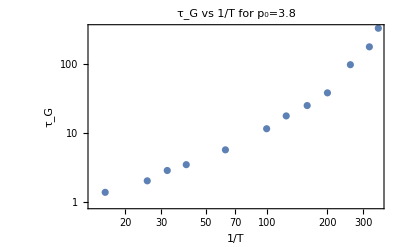

```mathematica
tauGPlot=ListLogLogPlot[Table[{1/temperatures[[1,T]],tau[[1,T]]},{T,Length[temperatures[[1]]]}],FrameLabel->{"1/T","τ_G"},ImageSize->400,PlotLabel->"τ_G vs 1/T for p_0="<>ToString[p0s[[1]]]]
```

```mathematica
results=Table[Grid[Partition[{fitsPlots[[p]],tauPlots[[p]],betaPlots[[p]],plateauPlots[[p]]},2]],{p,Length[p0s]}];
```

```mathematica
Table[Export["/home/chengling/Research/updates/06242024/SACfitting"<>ToString[p0s[[p]]]<>".jpeg",results[[p]],ImageResolution->800],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/06242024/SACfitting3.8.jpeg,/home/chengling/Research/updates/06242024/SACfitting3.825.jpeg,/home/chengling/Research/updates/06242024/SACfitting3.85.jpeg}

```mathematica
Table[Export["/home/chengling/Research/updates/05162024/relaxationModulus"<>ToString[p0s[[p]]]<>".jpeg",results[[p]],ImageResolution->800],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/05162024/relaxationModulus3.8.jpeg,/home/chengling/Research/updates/05162024/relaxationModulus3.825.jpeg,/home/chengling/Research/updates/05162024/relaxationModulus3.85.jpeg}

```mathematica
Export["/home/chengling/Research/updates/05092024/tauGPlot.jpeg",tauGPlot,ImageResolution->800]
```

/home/chengling/Research/updates/05092024/tauGPlot.jpeg

```mathematica
Export["/home/chengling/Research/updates/05092024/SACfit.jpeg",fittingPlotofSAC,ImageResolution->800]
```

/home/chengling/Research/updates/05092024/SACfit.jpeg

#### sacMean for copying

```mathematica
SACtimeMean
```

{{{7.11782×10^-6,7.04427×10^-6,6.968×10^-6,6.88922×10^-6,6.80789×10^-6,6.72407×10^-6,6.63787×10^-6,6.54936×10^-6,6.45871×10^-6,6.36608×10^-6,6.27144×10^-6,6.17501×10^-6,6.07676×10^-6,5.97686×10^-6,5.87546×10^-6,5.77274×10^-6,5.66863×10^-6,5.45773×10^-6,5.24373×10^-6,5.02772×10^-6,4.81104×10^-6,4.59485×10^-6,4.38034×10^-6,4.16862×10^-6,3.96185×10^-6,3.56168×10^-6,3.18751×10^-6,2.8448×10^-6,2.53733×10^-6,2.26727×10^-6,2.03494×10^-6,1.83918×10^-6,1.68565×10^-6,1.45222×10^-6,1.31518×10^-6,1.24323×10^-6,1.20692×10^-6,1.18332×10^-6,1.15978×10^-6,1.12952×10^-6,1.08914×10^-6,9.9782×10^-7,9.04779×10^-7,8.19103×10^-7,7.36228×10^-7,6.49192×10^-7,5.63381×10^-7,4.85023×10^-7,4.22781×10^-7,3.21986×10^-7,2.41404×10^-7,1.81375×10^-7,1.42149×10^-7,1.10269×10^-7,8.53632×10^-8,6.48061×10^-8,6.33025×10^-8,4.74408×10^-8,1.80142×10^-8,1.36794×10^-8,2.09873×10^-8,5.69666×10^-9,3.55625×10^-9,6.83842×10^-10,-1.29181×10^-8,-1.83183×10^-8,-6.04143×10^-9,-8.18561×10^-9,-1.05193×10^-8,-1.82261×10^-8,-5.55975×10^-9,5.6693×10^-9,4.34173×10^-9,-8.5479×10^-9,-1.49621×10^-8,-1.69054×10^-9,-1.10175×10^-8,-1.16073×10^-8,4.24245×10^-9,1.15714×10^-8,4.55665×10^-9,-1.69585×10^-9,1.00165×10^-8,8.4191×10^-9,-1.84528×10^-9,-7.53347×10^-10,-6.65389×10^-11,-8.23535×10^-9,-5.44658×10^-9,7.56659×10^-9,-5.12111×10^-9,-1.7971×10^-8,9.70136×10^-9,-9.89445×10^-9,1.17154×10^-8,1.81444×10^-9,1.31149×10^-9,3.92187×10^-10,9.71063×10^-9,-5.03553×10^-9,-6.37063×10^-9,-3.21874×10^-9,-9.37021×10^-9,-2.76994×10^-10,-2.36904×10^-9,4.78555×10^-10,6.26246×10^-9,2.036×10^-10,-4.99959×10^-9,-5.67132×10^-9,-4.24403×10^-9,-2.22428×10^-10,-4.92647×10^-10,-5.38804×10^-9,7.42635×10^-10,4.04288×10^-9,-1.88868×10^-9,-1.49587×10^-9,4.84055×10^-9,-2.84727×10^-11,-1.64173×10^-9,3.76691×10^-10,1.83431×10^-9,2.41344×10^-9,2.82117×10^-9,-4.76312×10^-9,2.16215×10^-9,-5.74366×10^-10,1.80853×10^-9,-3.31513×10^-9,2.83793×10^-10,-2.48389×10^-9,1.85708×10^-9,-1.18945×10^-10,2.40867×10^-9,-1.66947×10^-9,-2.09789×10^-10,5.81535×10^-10,1.18139×10^-9,5.4122×10^-9},{3.87684×10^-6,3.84875×10^-6,3.81898×10^-6,3.78754×10^-6,3.75445×10^-6,3.71977×10^-6,3.68354×10^-6,3.6458×10^-6,3.60661×10^-6,3.56603×10^-6,3.52409×10^-6,3.48087×10^-6,3.43641×10^-6,3.3908×10^-6,3.34408×10^-6,3.29633×10^-6,3.24735×10^-6,3.14725×10^-6,3.04412×10^-6,2.93852×10^-6,2.83112×10^-6,2.72246×10^-6,2.61313×10^-6,2.50376×10^-6,2.39517×10^-6,2.18155×10^-6,1.97613×10^-6,1.78232×10^-6,1.60298×10^-6,1.44002×10^-6,1.29449×10^-6,1.16722×10^-6,1.06258×10^-6,8.95695×10^-7,7.89446×10^-7,7.31307×10^-7,7.07226×10^-7,7.047×10^-7,7.13702×10^-7,7.2766×10^-7,7.41412×10^-7,7.59503×10^-7,7.56694×10^-7,7.2826×10^-7,6.78043×10^-7,6.14523×10^-7,5.49973×10^-7,4.94634×10^-7,4.52129×10^-7,3.83745×10^-7,3.28509×10^-7,2.78078×10^-7,2.27894×10^-7,1.89173×10^-7,1.67932×10^-7,1.52482×10^-7,1.28652×10^-7,9.06014×10^-8,7.64838×10^-8,5.61291×10^-8,3.51992×10^-8,2.54208×10^-8,2.56548×10^-8,3.11335×10^-8,2.22345×10^-8,5.00875×10^-9,5.03133×10^-9,1.75057×10^-9,-4.2788×10^-10,6.95965×10^-9,2.91717×10^-9,-2.26904×10^-9,4.96817×10^-9,6.06138×10^-9,-3.91388×10^-9,-9.86057×10^-9,-8.89178×10^-9,-3.60714×10^-9,-4.1213×10^-9,5.97097×10^-9,1.42907×10^-8,3.68556×10^-10,5.4259×10^-9,5.57087×10^-9,2.021×10^-10,-3.92471×10^-9,-3.73792×10^-9,-5.50621×10^-9,-5.84084×10^-9,-8.6149×10^-9,-1.27411×10^-8,-1.70094×10^-8,-1.02645×10^-8,-2.37719×10^-9,-1.12703×10^-8,-9.68085×10^-9,-4.11462×10^-9,-5.32625×10^-9,-3.03154×10^-9,5.72885×10^-9,3.98415×10^-9,-1.17842×10^-9,-6.50584×10^-10,1.12281×10^-9,-2.17032×10^-9,5.4994×10^-9,-5.2495×10^-9,-2.29605×10^-9,-3.10508×10^-9,-4.50211×10^-9,2.1579×10^-9,-6.03537×10^-9,-1.08168×10^-9,-1.28182×10^-9,6.07678×10^-10,-2.5926×10^-9,-5.68451×10^-9,3.03229×10^-9,-9.13744×10^-11,7.27644×10^-10,1.74913×10^-9,-6.45436×10^-10,-1.54553×10^-9,-6.94943×10^-10,4.10713×10^-9,3.04238×10^-9,-2.37701×10^-9,-2.20494×10^-9,-1.26075×10^-9,-4.08384×10^-9,2.25569×10^-9,2.18479×10^-10,7.2973×10^-10,1.24379×10^-9,2.0555×10^-9,-3.1888×10^-9,-1.0024×10^-9,-5.36955×10^-10,2.29251×10^-9,6.80547×10^-10},{2.86027×10^-6,2.84266×10^-6,2.82374×10^-6,2.80352×10^-6,2.78206×10^-6,2.75935×10^-6,2.73544×10^-6,2.71035×10^-6,2.6841×10^-6,2.65675×10^-6,2.62832×10^-6,2.59886×10^-6,2.5684×10^-6,2.537×10^-6,2.50471×10^-6,2.47158×10^-6,2.43746×10^-6,2.36735×10^-6,2.29464×10^-6,2.21973×10^-6,2.14301×10^-6,2.06492×10^-6,1.98591×10^-6,1.9064×10^-6,1.82697×10^-6,1.66954×10^-6,1.51641×10^-6,1.37027×10^-6,1.23323×10^-6,1.10703×10^-6,9.9298×10^-7,8.919×10^-7,8.07386×10^-7,6.7006×10^-7,5.79629×10^-7,5.28391×10^-7,5.07436×10^-7,5.07669×10^-7,5.21097×10^-7,5.40984×10^-7,5.62506×10^-7,5.99433×10^-7,6.17376×10^-7,6.09822×10^-7,5.78685×10^-7,5.31373×10^-7,4.79341×10^-7,4.31846×10^-7,3.9486×10^-7,3.34363×10^-7,2.89331×10^-7,2.57032×10^-7,2.29235×10^-7,2.0081×10^-7,1.78484×10^-7,1.60816×10^-7,1.39802×10^-7,1.04775×10^-7,8.2962×10^-8,6.6087×10^-8,4.39701×10^-8,3.29801×10^-8,2.56266×10^-8,1.79529×10^-8,1.15541×10^-8,-3.93955×10^-9,-5.71874×10^-9,-6.52939×10^-9,-2.98415×10^-9,-1.35343×10^-8,-7.46646×10^-9,-1.26091×10^-8,-8.75653×10^-9,-8.98531×10^-9,5.72397×10^-11,-1.89169×10^-9,-6.95633×10^-9,-8.2873×10^-9,-1.45324×10^-9,2.57752×10^-9,2.40255×10^-9,3.079×10^-9,4.20888×10^-9,1.48543×10^-9,-2.34368×10^-9,-7.55336×10^-9,6.74337×10^-10,1.86949×10^-10,-5.71606×10^-9,-3.36237×10^-9,1.16232×10^-9,1.11457×10^-9,1.84654×10^-9,5.85508×10^-9,-9.81745×10^-9,-6.0417×10^-9,-4.02512×10^-9,4.1293×10^-10,2.44589×10^-9,-1.23101×10^-9,4.4318×10^-9,2.77717×10^-9,1.8402×10^-9,-4.45104×10^-9,-2.87932×10^-9,2.19668×10^-9,3.2787×10^-9,2.79414×10^-9,-1.7192×10^-9,-3.7022×10^-9,3.94866×10^-9,-1.52084×10^-10,2.33862×10^-9,-1.67352×10^-9,-9.09852×10^-10,1.4932×10^-9,5.83792×10^-10,-5.64714×10^-10,2.99924×10^-9,-2.37723×10^-9,2.22011×10^-9,1.09738×10^-9,-2.61204×10^-9,-2.09653×10^-9,1.99173×10^-10,-5.0067×10^-10,-2.82445×10^-9,9.08453×10^-10,1.61716×10^-9,-1.0916×10^-9,-6.72175×10^-10,3.46078×10^-10,3.59579×10^-10,-1.52121×10^-9,-2.61401×10^-9,2.18071×10^-9,6.56389×10^-10,1.92396×10^-9,1.06958×10^-10,7.5301×10^-11},{1.1767×10^-6,1.17229×10^-6,1.1673×10^-6,1.16173×10^-6,1.15559×10^-6,1.1489×10^-6,1.14166×10^-6,1.13387×10^-6,1.12556×10^-6,1.11672×10^-6,1.10739×10^-6,1.09756×10^-6,1.08726×10^-6,1.07649×10^-6,1.06528×10^-6,1.05364×10^-6,1.04148×10^-6,1.0162×10^-6,9.89467×10^-7,9.61437×10^-7,9.32273×10^-7,9.02136×10^-7,8.71182×10^-7,8.3958×10^-7,8.07411×10^-7,7.42506×10^-7,6.77536×10^-7,6.1367×10^-7,5.51975×10^-7,4.93361×10^-7,4.38617×10^-7,3.88371×10^-7,3.44392×10^-7,2.69669×10^-7,2.16166×10^-7,1.82636×10^-7,1.66723×10^-7,1.65394×10^-7,1.7533×10^-7,1.93245×10^-7,2.16733×10^-7,2.66107×10^-7,3.08201×10^-7,3.31761×10^-7,3.33261×10^-7,3.16437×10^-7,2.90111×10^-7,2.63222×10^-7,2.42691×10^-7,2.15419×10^-7,2.03399×10^-7,1.96119×10^-7,1.86208×10^-7,1.73701×10^-7,1.61719×10^-7,1.50595×10^-7,1.41453×10^-7,1.25941×10^-7,1.12634×10^-7,9.90512×10^-8,8.90068×10^-8,7.85216×10^-8,6.94427×10^-8,6.02234×10^-8,5.54827×10^-8,4.26413×10^-8,3.15649×10^-8,2.41501×10^-8,2.00967×10^-8,1.51027×10^-8,1.13697×10^-8,8.46394×10^-9,8.29642×10^-9,6.53769×10^-9,6.29149×10^-9,4.46967×10^-9,-1.26603×10^-9,2.3305×10^-9,2.8601×10^-9,6.1805×10^-10,2.12312×10^-9,3.60055×10^-10,-3.3158×10^-9,-3.30417×10^-9,-3.10557×10^-9,-1.5361×10^-9,-1.10692×10^-10,2.73165×10^-9,4.42604×10^-9,1.64682×10^-9,1.18419×10^-9,-2.37084×10^-9,-2.49339×10^-9,-7.06164×10^-10,1.60525×10^-9,1.13495×10^-9,7.91396×10^-10,1.07925×10^-9,-6.16146×10^-10,-9.77889×10^-10,3.05978×10^-9,-4.56676×10^-10,1.76095×10^-9,4.31748×10^-10,-3.03974×10^-10,-9.95608×10^-10,-1.83442×10^-9,-2.16505×10^-9,1.41513×10^-9,9.53601×10^-10,1.79648×10^-9,-2.03042×10^-10,-9.88537×10^-10,-1.41134×10^-9,9.11771×10^-10,1.97779×10^-9,-6.8325×10^-10,-1.65237×10^-9,1.30157×10^-9,-8.43801×10^-10,7.51641×10^-10,3.72446×10^-10,1.57441×10^-9,9.4388×10^-10,-7.68072×10^-10,4.97596×10^-10,9.87798×10^-10,-4.42895×10^-10,6.1901×10^-10,6.97052×10^-10,-8.27477×10^-10,-2.43728×10^-10,9.21412×10^-10,9.91537×10^-10,9.21653×10^-10,-1.12019×10^-9,-4.02402×10^-10,1.68314×10^-9,1.21795×10^-9,5.27538×10^-11},{6.23708×10^-7,6.22068×10^-7,6.20105×10^-7,6.17825×10^-7,6.15231×10^-7,6.12327×10^-7,6.09117×10^-7,6.05604×10^-7,6.01792×10^-7,5.97688×10^-7,5.93297×10^-7,5.88624×10^-7,5.83678×10^-7,5.78465×10^-7,5.72992×10^-7,5.67265×10^-7,5.61232×10^-7,5.4859×10^-7,5.35066×10^-7,5.20734×10^-7,5.05669×10^-7,4.89954×10^-7,4.73666×10^-7,4.56889×10^-7,4.39625×10^-7,4.04404×10^-7,3.68537×10^-7,3.3266×10^-7,2.97365×10^-7,2.632×10^-7,2.30656×10^-7,2.00147×10^-7,1.72668×10^-7,1.24564×10^-7,8.81073×10^-8,6.35526×10^-8,5.02927×10^-8,4.70905×10^-8,5.2336×10^-8,6.41803×10^-8,8.13785×10^-8,1.19931×10^-7,1.56004×10^-7,1.79922×10^-7,1.87707×10^-7,1.81128×10^-7,1.65862×10^-7,1.48437×10^-7,1.34902×10^-7,1.1963×10^-7,1.18585×10^-7,1.21034×10^-7,1.18339×10^-7,1.10951×10^-7,1.03845×10^-7,9.89707×10^-8,9.57079×10^-8,8.93567×10^-8,8.24781×10^-8,7.55399×10^-8,7.09821×10^-8,6.58775×10^-8,6.03243×10^-8,5.68142×10^-8,5.43257×10^-8,4.68244×10^-8,4.21264×10^-8,3.49953×10^-8,3.24098×10^-8,2.75968×10^-8,2.45515×10^-8,2.02732×10^-8,1.82794×10^-8,1.43652×10^-8,1.15108×10^-8,1.01075×10^-8,8.66226×10^-9,7.26192×10^-9,5.79591×10^-9,4.9531×10^-9,4.55613×10^-9,3.5889×10^-9,9.24406×10^-10,-4.84573×10^-10,-2.02962×10^-9,6.12467×10^-10,5.74938×10^-10,1.62548×10^-9,3.49351×10^-9,2.8862×10^-9,3.64653×10^-9,3.29504×10^-9,1.08458×10^-9,-1.61891×10^-9,-1.22322×10^-9,1.14348×10^-9,3.28233×10^-11,-2.98678×10^-9,-2.53609×10^-9,-1.56234×10^-9,-6.83847×10^-10,-3.90421×10^-11,-7.8641×10^-10,3.59126×10^-10,5.8763×10^-11,-8.61431×10^-10,-2.56591×10^-10,-7.84075×10^-10,-5.92879×10^-10,4.95957×10^-10,8.12347×10^-12,-2.61616×10^-10,6.26595×10^-10,7.60961×10^-10,1.34016×10^-9,-1.97242×10^-9,9.38104×10^-10,2.17409×10^-9,-4.48393×10^-10,-6.68208×10^-10,-6.54533×10^-10,3.10755×10^-10,1.40572×10^-9,9.3958×10^-10,-9.91382×10^-10,1.41015×10^-10,1.42276×10^-9,4.41859×10^-10,-2.88891×10^-10,-4.3337×10^-10,7.69277×10^-10,4.85909×10^-10,-2.73622×10^-10,-5.77633×10^-10,3.08956×10^-10,9.70522×10^-10,8.54781×10^-10,-4.63223×10^-10,4.87212×10^-11,-2.75161×10^-10},{4.61242×10^-7,4.60218×10^-7,4.58953×10^-7,4.57448×10^-7,4.55705×10^-7,4.53727×10^-7,4.51515×10^-7,4.49074×10^-7,4.46407×10^-7,4.43518×10^-7,4.40413×10^-7,4.37093×10^-7,4.33564×10^-7,4.29829×10^-7,4.25895×10^-7,4.21766×10^-7,4.174×10^-7,4.08219×10^-7,3.98353×10^-7,3.87852×10^-7,3.76772×10^-7,3.65171×10^-7,3.53103×10^-7,3.40627×10^-7,3.27732×10^-7,3.0131×10^-7,2.74219×10^-7,2.4693×10^-7,2.19894×10^-7,1.93533×10^-7,1.68228×10^-7,1.44303×10^-7,1.22513×10^-7,8.39034×10^-8,5.39515×10^-8,3.31102×10^-8,2.11796×10^-8,1.74414×10^-8,2.07881×10^-8,2.9865×10^-8,4.38566×10^-8,7.62835×10^-8,1.08003×10^-7,1.30303×10^-7,1.38994×10^-7,1.34919×10^-7,1.22571×10^-7,1.07666×10^-7,9.59396×10^-8,8.40836×10^-8,8.6802×10^-8,9.22675×10^-8,9.08957×10^-8,8.38592×10^-8,7.74686×10^-8,7.42361×10^-8,7.26492×10^-8,6.93776×10^-8,6.61698×10^-8,6.18403×10^-8,5.81997×10^-8,5.479×10^-8,5.10524×10^-8,4.79114×10^-8,4.59675×10^-8,4.09723×10^-8,3.613×10^-8,3.29553×10^-8,2.7372×10^-8,2.70169×10^-8,2.23002×10^-8,1.98894×10^-8,1.83346×10^-8,1.47389×10^-8,1.17205×10^-8,1.00324×10^-8,8.37563×10^-9,6.64606×10^-9,4.28638×10^-9,3.30369×10^-9,2.22491×10^-9,1.35023×10^-9,3.80671×10^-12,-6.51562×10^-10,-1.01149×10^-9,-1.45312×10^-9,-6.16897×10^-11,-5.98486×10^-10,-8.26329×10^-10,-1.1719×10^-9,-1.80939×10^-10,-1.19025×10^-9,-1.6984×10^-9,-1.77634×10^-9,-1.34726×10^-9,-7.60768×10^-10,1.58585×10^-10,2.44673×10^-9,1.04559×10^-9,-1.65326×10^-10,-1.20922×10^-11,8.70856×10^-11,-4.88702×10^-10,-1.89556×10^-9,-1.26901×10^-9,-5.85919×10^-12,9.19131×10^-10,8.4088×10^-10,-5.11305×10^-10,-3.18019×10^-10,6.22648×10^-10,-3.35716×10^-10,1.17131×10^-9,-1.88371×10^-10,4.2636×10^-10,-6.94825×10^-10,5.61222×10^-10,-7.96788×10^-10,5.35389×10^-10,-8.53262×10^-10,-2.1849×10^-10,-8.17336×10^-10,-4.65405×10^-10,-5.86537×10^-10,-7.26606×10^-10,1.13143×10^-10,-1.73122×10^-9,6.25829×10^-10,7.17378×10^-10,3.10364×10^-10,1.19238×10^-10,-2.04229×10^-10,4.56143×10^-10,-2.57057×10^-10,2.41017×10^-10,4.49702×10^-10,1.93517×10^-10,7.00959×10^-11,2.53427×10^-10,2.98594×10^-10},{3.37704×10^-7,3.37082×10^-7,3.36281×10^-7,3.35304×10^-7,3.3415×10^-7,3.32823×10^-7,3.31323×10^-7,3.29653×10^-7,3.27815×10^-7,3.2581×10^-7,3.23644×10^-7,3.21317×10^-7,3.18834×10^-7,3.16197×10^-7,3.13409×10^-7,3.10475×10^-7,3.07363×10^-7,3.00798×10^-7,2.9371×10^-7,2.86134×10^-7,2.78106×10^-7,2.69666×10^-7,2.60856×10^-7,2.51718×10^-7,2.42231×10^-7,2.22717×10^-7,2.02579×10^-7,1.82159×10^-7,1.61781×10^-7,1.41764×10^-7,1.22395×10^-7,1.03939×10^-7,8.69521×10^-8,5.65136×10^-8,3.23969×10^-8,1.51523×10^-8,4.80422×10^-9,9.59064×10^-10,2.88998×10^-9,9.62537×10^-9,2.06383×10^-8,4.68824×10^-8,7.3343×10^-8,9.24781×10^-8,1.0041×10^-7,9.74442×10^-8,8.71194×10^-8,7.42573×10^-8,6.41457×10^-8,5.51111×10^-8,6.08851×10^-8,6.89621×10^-8,6.8656×10^-8,6.11468×10^-8,5.43029×10^-8,5.21963×10^-8,5.32652×10^-8,5.2506×10^-8,4.84453×10^-8,4.61876×10^-8,4.31404×10^-8,4.07474×10^-8,3.99517×10^-8,3.77895×10^-8,3.58562×10^-8,3.26144×10^-8,2.94709×10^-8,2.70698×10^-8,2.44991×10^-8,2.28817×10^-8,2.12179×10^-8,1.86872×10^-8,1.79048×10^-8,1.56413×10^-8,1.32342×10^-8,1.13717×10^-8,9.80699×10^-9,8.915×10^-9,7.5248×10^-9,7.39269×10^-9,6.23905×10^-9,6.09019×10^-9,5.1603×10^-9,4.54667×10^-9,4.36029×10^-9,4.17063×10^-9,3.73298×10^-9,2.86855×10^-9,1.72301×10^-9,3.59267×10^-10,1.09498×10^-9,2.24871×10^-9,1.79049×10^-9,2.63625×10^-9,2.39808×10^-9,2.3022×10^-9,1.29661×10^-9,2.4538×10^-9,2.53656×10^-9,1.73826×10^-9,8.42675×10^-10,-6.04626×10^-10,-5.67409×10^-10,-1.14654×10^-9,-8.83418×10^-10,-1.0457×10^-9,-4.23698×10^-10,-1.21098×10^-9,-1.9876×10^-10,6.29007×10^-10,6.87276×10^-10,1.50355×10^-9,8.44396×10^-10,-3.61956×10^-10,-2.08959×10^-10,-7.52991×10^-10,-4.37692×10^-10,-4.40324×10^-10,-1.05834×10^-9,4.74084×10^-10,-2.69894×10^-10,-1.17164×10^-10,-1.71113×10^-9,-1.44507×10^-9,1.09074×10^-9,9.87026×10^-10,-8.20491×10^-11,8.85788×10^-10,-5.24613×10^-13,-1.61573×10^-10,-5.89793×10^-10,-1.21535×10^-10,-2.27866×10^-10,1.30369×10^-10,1.72421×10^-10,-5.70451×10^-10,-9.00969×10^-10,-8.51409×10^-11,3.07719×10^-10,-4.77873×10^-10},{2.54083×10^-7,2.53696×10^-7,2.53173×10^-7,2.52516×10^-7,2.51725×10^-7,2.50801×10^-7,2.49746×10^-7,2.48561×10^-7,2.47247×10^-7,2.45807×10^-7,2.44242×10^-7,2.42553×10^-7,2.40744×10^-7,2.38816×10^-7,2.36773×10^-7,2.34617×10^-7,2.32322×10^-7,2.27467×10^-7,2.22205×10^-7,2.16559×10^-7,2.10557×10^-7,2.04229×10^-7,1.97603×10^-7,1.90708×10^-7,1.83526×10^-7,1.68697×10^-7,1.53304×10^-7,1.37604×10^-7,1.21848×10^-7,1.06276×10^-7,9.11128×10^-8,7.65631×10^-8,6.30481×10^-8,3.85983×10^-8,1.8874×10^-8,4.41511×10^-9,-4.6329×10^-9,-8.46276×10^-9,-7.5554×10^-9,-2.62038×10^-9,6.02202×10^-9,2.72884×10^-8,4.95387×10^-8,6.63826×10^-8,7.42453×10^-8,7.29417×10^-8,6.50832×10^-8,5.45665×10^-8,4.58948×10^-8,3.78756×10^-8,4.30396×10^-8,5.10337×10^-8,5.2353×10^-8,4.69625×10^-8,4.09629×10^-8,3.8567×10^-8,3.94218×10^-8,3.9669×10^-8,3.75426×10^-8,3.64512×10^-8,3.48993×10^-8,3.38832×10^-8,3.2635×10^-8,3.11624×10^-8,3.05398×10^-8,2.83632×10^-8,2.66062×10^-8,2.48301×10^-8,2.3424×10^-8,2.15961×10^-8,2.10636×10^-8,1.95896×10^-8,1.84171×10^-8,1.64105×10^-8,1.4594×10^-8,1.30622×10^-8,1.12323×10^-8,9.93295×10^-9,9.11345×10^-9,7.99172×10^-9,7.29328×10^-9,6.14801×10^-9,4.84437×10^-9,4.2001×10^-9,2.76303×10^-9,2.09941×10^-9,1.34946×10^-9,3.84979×10^-10,1.59333×10^-10,-2.66964×10^-10,-2.51848×10^-10,-5.60662×10^-10,-3.77213×10^-12,3.58737×10^-10,7.21882×10^-10,1.10752×10^-9,1.04621×10^-9,1.86209×10^-10,-6.87509×10^-10,-5.26487×10^-10,-1.8984×10^-10,-1.00559×10^-9,-6.63452×10^-10,-7.41945×10^-11,-4.27483×10^-10,4.00516×10^-11,-3.2534×10^-10,-5.89874×10^-10,-9.51675×10^-10,-4.13586×10^-10,-5.54942×10^-10,8.42128×10^-11,-2.19134×10^-10,-4.9813×10^-10,-8.26631×10^-10,-4.25362×10^-10,1.25213×10^-10,-7.78999×10^-10,1.63877×10^-9,1.0374×10^-9,1.05733×10^-9,-3.54803×10^-10,9.27736×10^-11,-5.61696×10^-10,2.34322×10^-10,2.64425×10^-10,2.94655×10^-10,2.85096×10^-10,-2.77763×10^-10,1.14971×10^-10,-7.13607×10^-12,-1.37208×10^-10,2.61062×10^-10,-3.75397×10^-10,-1.5389×10^-10,-5.60677×10^-11,-3.37545×10^-10,-2.07368×10^-10,1.14406×10^-11,3.42933×10^-10},{1.82706×10^-7,1.82479×10^-7,1.82154×10^-7,1.81732×10^-7,1.81213×10^-7,1.80599×10^-7,1.7989×10^-7,1.79087×10^-7,1.78191×10^-7,1.77203×10^-7,1.76125×10^-7,1.74957×10^-7,1.73702×10^-7,1.72359×10^-7,1.70932×10^-7,1.69422×10^-7,1.67811×10^-7,1.64393×10^-7,1.60673×10^-7,1.56669×10^-7,1.524×10^-7,1.47884×10^-7,1.43141×10^-7,1.38194×10^-7,1.33022×10^-7,1.22308×10^-7,1.1113×10^-7,9.96663×10^-8,8.80976×10^-8,7.65979×10^-8,6.53307×10^-8,5.44484×10^-8,4.42525×10^-8,2.56284×10^-8,1.03213×10^-8,-1.18655×10^-9,-8.69649×10^-9,-1.22697×10^-8,-1.21957×10^-8,-8.94261×10^-9,-2.662×10^-9,1.33669×10^-8,3.07706×10^-8,4.44056×10^-8,5.11788×10^-8,5.0632×10^-8,4.45965×10^-8,3.61228×10^-8,2.89403×10^-8,2.24758×10^-8,2.763×10^-8,3.53049×10^-8,3.68243×10^-8,3.23704×10^-8,2.78106×10^-8,2.67213×10^-8,2.80328×10^-8,2.84521×10^-8,2.61324×10^-8,2.593×10^-8,2.51877×10^-8,2.43605×10^-8,2.41913×10^-8,2.30778×10^-8,2.24947×10^-8,2.14704×10^-8,2.10648×10^-8,1.96956×10^-8,1.87969×10^-8,1.79592×10^-8,1.70736×10^-8,1.66299×10^-8,1.5799×10^-8,1.43742×10^-8,1.32762×10^-8,1.21008×10^-8,1.11387×10^-8,1.01967×10^-8,9.27551×10^-9,8.51279×10^-9,7.94071×10^-9,6.85003×10^-9,5.78647×10^-9,4.56498×10^-9,3.9316×10^-9,3.28549×10^-9,2.81146×10^-9,2.51566×10^-9,2.09411×10^-9,1.57304×10^-9,1.57418×10^-9,1.69673×10^-9,1.61245×10^-9,1.57351×10^-9,1.59624×10^-9,1.51809×10^-9,1.84469×10^-9,1.81155×10^-9,1.26432×10^-9,7.98299×10^-10,8.36187×10^-10,7.07716×10^-10,5.49756×10^-10,-1.67871×10^-11,-1.34754×10^-10,4.40054×10^-10,3.51258×10^-10,5.82908×10^-10,-6.05301×10^-11,-8.33797×10^-11,-2.17091×10^-10,-6.71164×10^-10,-3.24848×10^-10,-1.87328×10^-10,-8.58103×10^-10,-1.89848×10^-10,-9.68378×10^-10,3.95812×10^-10,1.59555×10^-11,-2.77602×10^-10,-2.00385×10^-10,-3.78525×10^-10,-8.32379×10^-10,-7.01421×10^-10,5.85518×10^-11,-3.36471×10^-10,-7.24146×10^-10,-8.84433×10^-10,4.14164×10^-10,5.03511×10^-10,5.94563×10^-10,3.19563×10^-10,6.56757×10^-10,1.31081×10^-10,5.01051×10^-10,1.94132×10^-10,5.39157×10^-11,-1.77648×10^-10,6.01131×10^-10,-2.71827×10^-10},{1.40591×10^-7,1.40443×10^-7,1.40219×10^-7,1.3992×10^-7,1.39545×10^-7,1.39096×10^-7,1.38573×10^-7,1.37977×10^-7,1.37307×10^-7,1.36566×10^-7,1.35754×10^-7,1.34872×10^-7,1.33922×10^-7,1.32903×10^-7,1.31817×10^-7,1.30667×10^-7,1.29436×10^-7,1.2682×10^-7,1.23964×10^-7,1.20883×10^-7,1.17589×10^-7,1.14098×10^-7,1.10424×10^-7,1.06583×10^-7,1.02559×10^-7,9.42024×10^-8,8.54489×10^-8,7.64378×10^-8,6.73078×10^-8,5.81944×10^-8,4.9228×10^-8,4.05297×10^-8,3.2331×10^-8,1.72639×10^-8,4.74093×10^-9,-4.80714×10^-9,-1.117×10^-8,-1.4347×10^-8,-1.45268×10^-8,-1.20601×10^-8,-7.02869×10^-9,6.08303×10^-9,2.061×10^-8,3.22001×10^-8,3.81136×10^-8,3.77639×10^-8,3.25361×10^-8,2.49756×10^-8,1.83597×10^-8,1.22361×10^-8,1.73034×10^-8,2.55522×10^-8,2.81917×10^-8,2.43379×10^-8,1.94232×10^-8,1.78753×10^-8,1.95071×10^-8,2.056×10^-8,1.80206×10^-8,1.81948×10^-8,1.84706×10^-8,1.74052×10^-8,1.7206×10^-8,1.66595×10^-8,1.57996×10^-8,1.54941×10^-8,1.52445×10^-8,1.43397×10^-8,1.40981×10^-8,1.35622×10^-8,1.28384×10^-8,1.31055×10^-8,1.23721×10^-8,1.15059×10^-8,1.09451×10^-8,1.00609×10^-8,9.51888×10^-9,9.00312×10^-9,8.46688×10^-9,8.02934×10^-9,7.644×10^-9,6.37694×10^-9,5.74875×10^-9,5.02559×10^-9,4.6675×10^-9,4.07234×10^-9,3.44986×10^-9,3.29956×10^-9,3.11482×10^-9,2.56803×10^-9,2.19624×10^-9,2.06416×10^-9,1.99937×10^-9,1.63792×10^-9,1.23474×10^-9,9.4842×10^-10,9.11155×10^-10,4.40075×10^-10,5.14424×10^-10,4.76307×10^-10,2.58874×10^-10,1.64647×10^-10,2.83894×10^-10,1.82406×10^-10,-8.9244×10^-11,-1.11737×10^-10,-9.66955×10^-11,-1.53855×10^-10,-1.18502×10^-10,2.03445×10^-12,-4.07641×10^-11,3.73431×10^-10,2.53045×10^-10,7.95454×10^-11,4.21666×10^-11,-8.38187×10^-10,-3.22814×10^-10,2.13571×10^-10,1.15614×10^-10,5.05196×10^-10,1.89809×10^-10,2.84633×10^-10,2.62884×10^-11,-1.68182×10^-11,-1.04514×10^-10,1.57878×10^-10,-1.78986×10^-10,-6.81621×10^-10,-7.08101×10^-10,3.11908×10^-12,2.16242×10^-10,2.18968×10^-10,2.23461×10^-11,3.9895×10^-11,-4.21456×10^-10,7.37076×10^-10,2.28933×10^-10,-1.2697×10^-10,-3.69003×10^-10,-4.28402×10^-11},{1.07568×10^-7,1.07471×10^-7,1.07316×10^-7,1.07102×10^-7,1.0683×10^-7,1.06501×10^-7,1.06114×10^-7,1.05671×10^-7,1.05172×10^-7,1.04617×10^-7,1.04007×10^-7,1.03343×10^-7,1.02625×10^-7,1.01855×10^-7,1.01033×10^-7,1.0016×10^-7,9.92243×10^-8,9.7233×10^-8,9.50548×10^-8,9.26994×10^-8,9.0177×10^-8,8.74983×10^-8,8.46746×10^-8,8.17179×10^-8,7.86133×10^-8,7.21525×10^-8,6.53626×10^-8,5.83496×10^-8,5.12193×10^-8,4.4076×10^-8,3.70206×10^-8,3.01484×10^-8,2.36362×10^-8,1.15977×10^-8,1.48088×10^-9,-6.34855×10^-9,-1.16929×10^-8,-1.45212×10^-8,-1.49541×10^-8,-1.3247×10^-8,-9.4332×10^-9,7.77337×10^-10,1.23623×10^-8,2.17921×10^-8,2.67692×10^-8,2.67008×10^-8,2.25924×10^-8,1.64477×10^-8,1.09471×10^-8,5.80405×10^-9,1.02074×10^-8,1.74823×10^-8,1.99898×10^-8,1.67673×10^-8,1.24198×10^-8,1.10315×10^-8,1.27737×10^-8,1.43375×10^-8,1.20241×10^-8,1.19684×10^-8,1.23581×10^-8,1.15047×10^-8,1.13732×10^-8,1.17253×10^-8,1.12292×10^-8,1.05394×10^-8,1.03532×10^-8,9.70735×10^-9,9.77867×10^-9,9.10043×10^-9,9.18909×10^-9,8.88013×10^-9,8.77072×10^-9,8.01065×10^-9,7.60383×10^-9,7.34926×10^-9,7.02938×10^-9,6.52671×10^-9,6.21562×10^-9,6.05428×10^-9,5.74347×10^-9,5.31386×10^-9,4.70388×10^-9,4.45228×10^-9,4.24816×10^-9,3.67582×10^-9,3.40411×10^-9,3.10644×10^-9,2.8369×10^-9,2.66016×10^-9,2.2843×10^-9,2.26652×10^-9,1.95394×10^-9,1.7201×10^-9,1.46394×10^-9,1.28528×10^-9,1.32578×10^-9,9.14837×10^-10,5.74349×10^-10,5.25935×10^-10,4.53904×10^-10,4.88189×10^-10,7.38742×10^-10,5.13019×10^-10,5.5349×10^-10,3.11299×10^-10,1.47426×10^-10,2.35478×10^-11,1.51028×10^-10,2.89134×10^-10,4.4951×10^-11,-2.10124×10^-11,2.02879×10^-10,4.90094×10^-10,5.47736×10^-10,5.25212×10^-10,3.41081×10^-11,-3.31686×10^-10,-4.33064×10^-10,-3.36614×10^-10,-1.00393×10^-10,-1.43664×10^-10,2.33759×10^-10,9.80951×10^-11,5.79498×10^-10,4.35104×10^-10,2.81504×10^-10,-4.22663×10^-11,1.29469×10^-10,-1.75361×10^-10,-8.07019×10^-10,-5.59713×10^-10,-2.72335×10^-10,-1.49409×10^-10,-4.44911×10^-10,4.39746×10^-10,1.63591×10^-10,-6.15883×10^-10,-8.21166×10^-11,2.54679×10^-10},{8.36129×10^-8,8.35491×10^-8,8.344×10^-8,8.32856×10^-8,8.30862×10^-8,8.28421×10^-8,8.25535×10^-8,8.22208×10^-8,8.18442×10^-8,8.14243×10^-8,8.09614×10^-8,8.04562×10^-8,7.99091×10^-8,7.93207×10^-8,7.86918×10^-8,7.80231×10^-8,7.73055×10^-8,7.57757×10^-8,7.40988×10^-8,7.2282×10^-8,7.03329×10^-8,6.82595×10^-8,6.60705×10^-8,6.37747×10^-8,6.13597×10^-8,5.63247×10^-8,5.1018×10^-8,4.55211×10^-8,3.99162×10^-8,3.42847×10^-8,2.87056×10^-8,2.32541×10^-8,1.80666×10^-8,8.43482×10^-9,2.75725×10^-10,-6.10039×10^-9,-1.05151×10^-8,-1.29219×10^-8,-1.33993×10^-8,-1.21374×10^-8,-9.14123×10^-9,-9.79935×10^-10,8.40628×10^-9,1.61062×10^-8,2.0174×10^-8,2.00579×10^-8,1.65438×10^-8,1.12942×10^-8,6.60988×10^-9,2.42103×10^-9,6.7216×10^-9,1.34721×10^-8,1.56827×10^-8,1.25773×10^-8,8.60289×10^-9,7.60593×10^-9,9.42676×10^-9,1.06957×10^-8,8.38112×10^-9,8.76156×10^-9,9.2034×10^-9,8.64513×10^-9,8.6161×10^-9,8.40133×10^-9,8.03517×10^-9,8.23975×10^-9,8.00563×10^-9,7.66853×10^-9,7.40574×10^-9,7.37459×10^-9,6.95082×10^-9,6.8458×10^-9,6.80025×10^-9,6.81034×10^-9,6.50072×10^-9,6.47065×10^-9,6.26558×10^-9,5.80695×10^-9,5.61232×10^-9,5.56865×10^-9,5.40388×10^-9,5.03744×10^-9,4.90279×10^-9,4.54931×10^-9,4.34306×10^-9,3.91264×10^-9,3.75068×10^-9,3.5983×10^-9,3.4619×10^-9,2.96911×10^-9,2.41595×10^-9,2.18111×10^-9,1.99054×10^-9,1.73449×10^-9,1.46978×10^-9,1.35976×10^-9,1.25289×10^-9,9.89944×10^-10,7.87036×10^-10,5.68698×10^-10,4.02026×10^-10,3.89212×10^-10,1.87108×10^-10,3.36129×10^-11,3.16677×10^-11,-4.22152×10^-11,7.08698×10^-12,1.03172×10^-10,1.87406×10^-10,1.90314×10^-10,3.11065×10^-10,2.6661×10^-10,4.14468×10^-10,5.84347×10^-10,5.78841×10^-10,1.8151×10^-10,-3.51139×10^-10,-3.14246×10^-10,-2.5619×10^-10,3.49621×10^-10,3.65676×10^-10,-8.02677×10^-11,-1.24361×10^-10,3.32622×10^-11,-5.6201×10^-12,-1.62225×10^-10,-3.57165×10^-10,-4.13765×10^-11,2.47883×10^-10,-5.12874×10^-10,2.43536×10^-10,-3.83758×10^-10,-7.34841×10^-11,-5.99182×10^-10,3.67172×10^-10,-3.49528×10^-12,-9.7182×10^-11,-2.48948×10^-10,-2.70896×10^-10,-1.57603×10^-10},{5.97491×10^-8,5.97116×10^-8,5.96413×10^-8,5.95385×10^-8,5.94032×10^-8,5.92356×10^-8,5.90359×10^-8,5.88043×10^-8,5.85411×10^-8,5.82464×10^-8,5.79207×10^-8,5.75642×10^-8,5.71774×10^-8,5.67607×10^-8,5.63144×10^-8,5.58391×10^-8,5.53283×10^-8,5.42375×10^-8,5.30391×10^-8,5.1738×10^-8,5.03395×10^-8,4.88491×10^-8,4.72729×10^-8,4.56171×10^-8,4.38713×10^-8,4.02242×10^-8,3.63671×10^-8,3.23578×10^-8,2.82549×10^-8,2.41166×10^-8,2.00001×10^-8,1.59606×10^-8,1.20944×10^-8,4.87002×10^-9,-1.32406×10^-9,-6.24281×10^-9,-9.73487×10^-9,-1.17448×10^-8,-1.23104×10^-8,-1.15547×10^-8,-9.45419×10^-9,-3.5018×10^-9,3.58924×10^-9,9.60659×10^-9,1.29973×10^-8,1.32158×10^-8,1.07316×10^-8,6.73034×10^-9,2.94004×10^-9,-8.01728×10^-10,2.29389×10^-9,7.89088×10^-9,1.02084×10^-8,8.05389×10^-9,4.74605×10^-9,3.64206×10^-9,5.01615×10^-9,6.17287×10^-9,4.50863×10^-9,4.89838×10^-9,4.82441×10^-9,4.24072×10^-9,4.81222×10^-9,4.61497×10^-9,4.37348×10^-9,4.46869×10^-9,4.10546×10^-9,4.26747×10^-9,4.13053×10^-9,4.07604×10^-9,3.98484×10^-9,3.77283×10^-9,3.91196×10^-9,3.77542×10^-9,3.67617×10^-9,3.65268×10^-9,3.5821×10^-9,3.42194×10^-9,3.40598×10^-9,3.31426×10^-9,3.20669×10^-9,3.05229×10^-9,2.99558×10^-9,2.79397×10^-9,2.6874×10^-9,2.57456×10^-9,2.46068×10^-9,2.31231×10^-9,2.26596×10^-9,2.04186×10^-9,1.89483×10^-9,1.71261×10^-9,1.565×10^-9,1.44929×10^-9,1.37772×10^-9,1.3369×10^-9,1.23246×10^-9,1.04859×10^-9,9.30886×10^-10,8.58324×10^-10,7.48611×10^-10,7.24716×10^-10,6.63025×10^-10,6.97668×10^-10,5.86683×10^-10,4.11787×10^-10,3.60166×10^-10,2.74586×10^-10,3.45118×10^-10,2.9249×10^-10,1.78507×10^-10,2.35133×10^-10,3.18128×10^-10,2.7175×10^-10,1.42284×10^-10,6.32506×10^-11,-8.77103×10^-11,-4.29351×10^-11,-2.99112×10^-11,-9.16814×10^-11,-9.09944×10^-11,-2.54963×10^-11,-2.53236×10^-10,-3.83246×10^-10,-2.83473×10^-10,-2.77985×10^-10,-2.74861×10^-10,-2.69112×10^-10,-1.59882×10^-10,-3.23163×10^-11,-6.29675×10^-11,1.70909×10^-10,-5.45242×10^-11,8.79539×10^-11,6.86818×10^-11,2.07173×10^-11,4.47566×10^-11,-1.17662×10^-10,8.32866×10^-11,-5.42959×10^-11},{3.88389×10^-8,3.88204×10^-8,3.87811×10^-8,3.87211×10^-8,3.86405×10^-8,3.85392×10^-8,3.84175×10^-8,3.82755×10^-8,3.81133×10^-8,3.7931×10^-8,3.7729×10^-8,3.75072×10^-8,3.7266×10^-8,3.70057×10^-8,3.67264×10^-8,3.64285×10^-8,3.61077×10^-8,3.54214×10^-8,3.46657×10^-8,3.38435×10^-8,3.29579×10^-8,3.20123×10^-8,3.10103×10^-8,2.99558×10^-8,2.88416×10^-8,2.65083×10^-8,2.40317×10^-8,2.14475×10^-8,1.87925×10^-8,1.61035×10^-8,1.34171×10^-8,1.07687×10^-8,8.21787×10^-9,3.41834×10^-9,-7.50877×10^-10,-4.11978×10^-9,-6.57659×10^-9,-8.07157×10^-9,-8.61598×10^-9,-8.27811×10^-9,-7.02432×10^-9,-3.28161×10^-9,1.3513×10^-9,5.39562×10^-9,7.76901×10^-9,8.03537×10^-9,6.44044×10^-9,3.74099×10^-9,1.09755×10^-9,-1.60256×10^-9,5.38139×10^-10,4.59067×10^-9,6.33253×10^-9,4.76382×10^-9,2.3293×10^-9,1.63009×10^-9,2.87734×10^-9,3.90237×10^-9,2.30309×10^-9,2.53625×10^-9,2.73727×10^-9,2.26054×10^-9,2.41349×10^-9,2.38889×10^-9,2.36729×10^-9,2.54823×10^-9,2.49885×10^-9,2.45379×10^-9,2.44715×10^-9,2.31388×10^-9,2.31683×10^-9,2.26236×10^-9,2.25546×10^-9,2.2293×10^-9,2.1673×10^-9,2.15459×10^-9,2.07306×10^-9,2.13359×10^-9,2.06641×10^-9,2.0603×10^-9,2.04721×10^-9,1.97938×10^-9,1.89737×10^-9,1.88805×10^-9,1.86714×10^-9,1.81432×10^-9,1.80455×10^-9,1.75721×10^-9,1.71112×10^-9,1.64818×10^-9,1.64991×10^-9,1.56686×10^-9,1.50316×10^-9,1.45739×10^-9,1.41285×10^-9,1.38952×10^-9,1.33126×10^-9,1.26191×10^-9,1.18122×10^-9,1.08094×10^-9,1.0405×10^-9,9.65114×10^-10,9.31846×10^-10,9.02459×10^-10,8.59867×10^-10,7.96931×10^-10,7.36513×10^-10,6.16057×10^-10,5.92602×10^-10,5.51848×10^-10,5.04471×10^-10,4.65693×10^-10,4.18718×10^-10,3.99288×10^-10,3.33822×10^-10,3.34781×10^-10,2.87155×10^-10,2.75347×10^-10,2.20595×10^-10,1.70643×10^-10,1.84509×10^-10,1.2278×10^-10,6.66043×10^-11,-1.81498×10^-11,-3.91288×10^-11,-7.95108×10^-11,-6.70525×10^-11,-1.10459×10^-10,-1.09047×10^-10,-5.89735×10^-11,6.3805×10^-11,1.25479×10^-10,9.27219×10^-11,-3.80544×10^-11,-1.4639×10^-10,-1.97675×10^-10,-8.31272×10^-11,-7.9168×10^-11,-1.66742×10^-10,-1.63877×10^-10,-1.20395×10^-10,-1.66665×10^-11,-5.09923×10^-11,-3.57609×10^-10}}}